```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"fourdiff.wl"
```

### EOM

```mathematica
eqf=Derivative[0,1][f][t,x]-(dim-3)((f[t,x] (-1+1/ia2[t,x]))/x);
eqia2=Derivative[0,1][ia2][t,x]-(dim-3)/x+ia2[t,x]*(8(dim-3)+(dim-2)^3*(U[t,x]^2+V[t,x]^2))/(8*x);
eqU=Derivative[0,1][U][t,x]-(f[t,x] ((dim-2-2(dim-3)/ia2[t,x]) U[t,x]+(dim-2)*V[t,x])-2*x*Derivative[1,0][U][t,x])/(2*x*(f[t,x]+x));
eqV=Derivative[0,1][V][t,x]-(f[t,x] ((dim-2-2(dim-3)/ia2[t,x]) V[t,x]+(dim-2)*U[t,x])+2*x*Derivative[1,0][V][t,x])/(2*x*(f[t,x]-x));
constr=Derivative[1,0][ia2][t,x]+dim-3-ia2[t,x]*(dim-3+(dim-2)^3*((x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2)/(8*x));
```

```mathematica
eomall0=x*{eqf,eqia2,eqU,eqV,constr};
```

```mathematica
eomall={eqf,eqia2,eqU,eqV,constr};
```

### Linearized equations

```mathematica
linearize={f[t,x]->f[t,x]+epsilon delf[t,x],ia2[t,x]->ia2[t,x]+epsilon delia2[t,x],U[t,x]->U[t,x]+epsilon delU[t,x],V[t,x]->V[t,x]+epsilon delV[t,x],Derivative[1,0][f][t,x]->epsilon Derivative[1,0][delf][t,x]+Derivative[1,0][f][t,x],Derivative[1,0][ia2][t,x]->epsilon Derivative[1,0][delia2][t,x]+Derivative[1,0][ia2][t,x],Derivative[1,0][U][t,x]->epsilon Derivative[1,0][delU][t,x]+Derivative[1,0][U][t,x],Derivative[1,0][V][t,x]->epsilon Derivative[1,0][delV][t,x]+Derivative[1,0][V][t,x],Derivative[0,1][f][t,x]->epsilon Derivative[0,1][delf][t,x]+Derivative[0,1][f][t,x],Derivative[0,1][ia2][t,x]->epsilon Derivative[0,1][delia2][t,x]+Derivative[0,1][ia2][t,x],Derivative[0,1][U][t,x]->epsilon Derivative[0,1][delU][t,x]+Derivative[0,1][U][t,x],Derivative[0,1][V][t,x]->epsilon Derivative[0,1][delV][t,x]+Derivative[0,1][V][t,x]};
```

```mathematica
leqf=D[eqf/.linearize,epsilon]/.epsilon->0//Simplify
```

-((-3+dim) delf[t,x] (-1+1/ia2[t,x]))/x+((-3+dim) delia2[t,x] f[t,x])/(x ia2[t,x]^2)+delf^(0,1)[t,x]

```mathematica
leqia2=D[eqia2/.linearize,epsilon]/.epsilon->0//Simplify
```

((-2+dim)^3 ia2[t,x] (delU[t,x] U[t,x]+delV[t,x] V[t,x]))/(4 x)+(delia2[t,x] (8 (-3+dim)+(-2+dim)^3 (U[t,x]^2+V[t,x]^2)))/(8 x)+delia2^(0,1)[t,x]

```mathematica
leqU=D[eqU/.linearize,epsilon]/.epsilon->0//Simplify
```

delU^(0,1)[t,x]-(f[t,x] ((-2+dim) delV[t,x]+delU[t,x] (-2+dim+(6-2 dim)/ia2[t,x])+(2 (-3+dim) delia2[t,x] U[t,x])/ia2[t,x]^2)+delf[t,x] ((-2+dim+(6-2 dim)/ia2[t,x]) U[t,x]+(-2+dim) V[t,x])-2 x delU^(1,0)[t,x])/(2 x (x+f[t,x]))+(delf[t,x] (f[t,x] ((-2+dim+(6-2 dim)/ia2[t,x]) U[t,x]+(-2+dim) V[t,x])-2 x U^(1,0)[t,x]))/(2 x (x+f[t,x])^2)

```mathematica
leqV=D[eqV/.linearize,epsilon]/.epsilon->0//Simplify
```

delV^(0,1)[t,x]-(delf[t,x] ((-2+dim) U[t,x]+(-2+dim+(6-2 dim)/ia2[t,x]) V[t,x])+f[t,x] ((-2+dim) delU[t,x]+delV[t,x] (-2+dim+(6-2 dim)/ia2[t,x])+(2 (-3+dim) delia2[t,x] V[t,x])/ia2[t,x]^2)+2 x delV^(1,0)[t,x])/(2 x (-x+f[t,x]))+(delf[t,x] (f[t,x] (-(2 (-3+dim) V[t,x])/ia2[t,x]+(-2+dim) (U[t,x]+V[t,x]))+2 x V^(1,0)[t,x]))/(2 x (x-f[t,x])^2)

```mathematica
lconstr=D[constr/.linearize,epsilon]/.epsilon->0//Simplify
```

-((-2+dim)^3 ia2[t,x] (2 delU[t,x] (x+f[t,x]) U[t,x]+2 delV[t,x] (x-f[t,x]) V[t,x]+delf[t,x] (U[t,x]^2-V[t,x]^2)))/(8 x)-delia2[t,x] (-3+dim+((-2+dim)^3 ((x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2))/(8 x))+delia2^(1,0)[t,x]

### Eigenvalue problem

```mathematica
eigenf=leqf
```

-((-3+dim) delf[t,x] (-1+1/ia2[t,x]))/x+((-3+dim) delia2[t,x] f[t,x])/(x ia2[t,x]^2)+delf^(0,1)[t,x]

```mathematica
Solve[eigenf==0,Derivative[0,1][delf][t,x]]
```

{{delf^(0,1)[t,x]→-((-3+dim) (delia2[t,x] f[t,x]-delf[t,x] ia2[t,x]+delf[t,x] ia2[t,x]^2))/(x ia2[t,x]^2)}}

```mathematica
eigenia2=leqia2;
```

```mathematica
eigenU=leqU/.Derivative[1,0][delU][t,x]->(Derivative[1,0][delU][t,x]+lambda delU[t,x])//FullSimplify
```

delU^(0,1)[t,x]-1/(2 x (x+f[t,x]))(f[t,x] ((-2+dim) delV[t,x]+delU[t,x] (-2+dim+(6-2 dim)/ia2[t,x])+(2 (-3+dim) delia2[t,x] U[t,x])/ia2[t,x]^2)+delf[t,x] ((-2+dim+(6-2 dim)/ia2[t,x]) U[t,x]+(-2+dim) V[t,x])-2 x (lambda delU[t,x]+delU^(1,0)[t,x]))+(delf[t,x] (f[t,x] ((-2+dim+(6-2 dim)/ia2[t,x]) U[t,x]+(-2+dim) V[t,x])-2 x U^(1,0)[t,x]))/(2 x (x+f[t,x])^2)

```mathematica
SetOptions[$Output,PageWidth->62]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→62,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
Solve[eigenU==0,Derivative[0,1][delU][t,x]]//FullSimplify//Together//FullSimplify
```

{{delU^(0,1)[t,x]→1/(2 x (x+f[t,x])^2 ia2[t,x]^2)((-2+dim) delV[t,x] f[t,x] (x+f[t,x]) ia2[t,x]^2-delU[t,x] (x+f[t,x]) ia2[t,x] (2 lambda x ia2[t,x]+f[t,x] (2 (-3+dim)-(-2+dim) ia2[t,x]))-6 x delia2[t,x] f[t,x] U[t,x]+2 dim x delia2[t,x] f[t,x] U[t,x]-6 delia2[t,x] f[t,x]^2 U[t,x]+2 dim delia2[t,x] f[t,x]^2 U[t,x]+6 x delf[t,x] ia2[t,x] U[t,x]-2 dim x delf[t,x] ia2[t,x] U[t,x]-2 x delf[t,x] ia2[t,x]^2 U[t,x]+dim x delf[t,x] ia2[t,x]^2 U[t,x]-2 x delf[t,x] ia2[t,x]^2 V[t,x]+dim x delf[t,x] ia2[t,x]^2 V[t,x]-2 x^2 ia2[t,x]^2 delU^(1,0)[t,x]-2 x f[t,x] ia2[t,x]^2 delU^(1,0)[t,x]+2 x delf[t,x] ia2[t,x]^2 U^(1,0)[t,x])}}

```mathematica
%/.{f[t,x]->fB[i],delV[t,x]->v[i],delU[t,x]->u[i],ia2[t,x]->ia2B[i],delia2[t,x]->ia2[i],U[t,x]->uB[i],V[t,x]->vB[i],delf[t,x]->f[i],lambda->lamb,Derivative[1,0][delU][t,x]->dudtau[i],Derivative[1,0][U][t,x]->dudtauB[i],dim->d}//FortranForm
```

List(List(Rule(Derivative(0,1)(delU)(t,x),
     -    (-2*x**2*dudtau(i)*ia2B(i)**2 + 
     -       2*x*dudtauB(i)*f(i)*ia2B(i)**2 - 
     -       2*x*dudtau(i)*fB(i)*ia2B(i)**2 - 
     -       (x + fB(i))*ia2B(i)*
     -        (2*lamb*x*ia2B(i) + 
     -          fB(i)*(2*(-3 + d) - (-2 + d)*ia2B(i)))*u(i) - 
     -       6*x*fB(i)*ia2(i)*uB(i) + 
     -       2*d*x*fB(i)*ia2(i)*uB(i) - 
     -       6*fB(i)**2*ia2(i)*uB(i) + 
     -       2*d*fB(i)**2*ia2(i)*uB(i) + 
     -       6*x*f(i)*ia2B(i)*uB(i) - 
     -       2*d*x*f(i)*ia2B(i)*uB(i) - 
     -       2*x*f(i)*ia2B(i)**2*uB(i) + 
     -       d*x*f(i)*ia2B(i)**2*uB(i) + 
     -       (-2 + d)*fB(i)*(x + fB(i))*ia2B(i)**2*v(i) - 
     -       2*x*f(i)*ia2B(i)**2*vB(i) + 
     -       d*x*f(i)*ia2B(i)**2*vB(i))/
     -     (2.*x*(x + fB(i))**2*ia2B(i)**2))))

```mathematica
eigenV=leqV/.Derivative[1,0][delV][t,x]->Derivative[1,0][delV][t,x]+lambda delV[t,x]
```

delV^(0,1)[t,x]-1/(2 x (-x+f[t,x]))(delf[t,x] ((-2+dim) U[t,x]+(-2+dim+(6-2 dim)/ia2[t,x]) V[t,x])+f[t,x] ((-2+dim) delU[t,x]+delV[t,x] (-2+dim+(6-2 dim)/ia2[t,x])+(2 (-3+dim) delia2[t,x] V[t,x])/ia2[t,x]^2)+2 x (lambda delV[t,x]+delV^(1,0)[t,x]))+(delf[t,x] (f[t,x] (-(2 (-3+dim) V[t,x])/ia2[t,x]+(-2+dim) (U[t,x]+V[t,x]))+2 x V^(1,0)[t,x]))/(2 x (x-f[t,x])^2)

```mathematica
eigenV=leqV/.Derivative[1,0][delV][t,x]->(Derivative[1,0][delV][t,x]+lambda delV[t,x])
```

delV^(0,1)[t,x]-1/(2 x (-x+f[t,x]))(delf[t,x] ((-2+dim) U[t,x]+(-2+dim+(6-2 dim)/ia2[t,x]) V[t,x])+f[t,x] ((-2+dim) delU[t,x]+delV[t,x] (-2+dim+(6-2 dim)/ia2[t,x])+(2 (-3+dim) delia2[t,x] V[t,x])/ia2[t,x]^2)+2 x (lambda delV[t,x]+delV^(1,0)[t,x]))+(delf[t,x] (f[t,x] (-(2 (-3+dim) V[t,x])/ia2[t,x]+(-2+dim) (U[t,x]+V[t,x]))+2 x V^(1,0)[t,x]))/(2 x (x-f[t,x])^2)

```mathematica
SetOptions[$Output,PageWidth->62]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→62,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
Solve[eigenV==0,Derivative[0,1][delV][t,x]]//FullSimplify//Together//FullSimplify
```

{{delV^(0,1)[t,x]→-1/(2 x (x-f[t,x])^2 ia2[t,x]^2)((-2+dim) delU[t,x] (x-f[t,x]) f[t,x] ia2[t,x]^2+delV[t,x] (x-f[t,x]) ia2[t,x] (2 lambda x ia2[t,x]+f[t,x] (6-2 dim+(-2+dim) ia2[t,x]))-2 x delf[t,x] ia2[t,x]^2 U[t,x]+dim x delf[t,x] ia2[t,x]^2 U[t,x]-6 x delia2[t,x] f[t,x] V[t,x]+2 dim x delia2[t,x] f[t,x] V[t,x]+6 delia2[t,x] f[t,x]^2 V[t,x]-2 dim delia2[t,x] f[t,x]^2 V[t,x]+6 x delf[t,x] ia2[t,x] V[t,x]-2 dim x delf[t,x] ia2[t,x] V[t,x]-2 x delf[t,x] ia2[t,x]^2 V[t,x]+dim x delf[t,x] ia2[t,x]^2 V[t,x]+2 x^2 ia2[t,x]^2 delV^(1,0)[t,x]-2 x f[t,x] ia2[t,x]^2 delV^(1,0)[t,x]+2 x delf[t,x] ia2[t,x]^2 V^(1,0)[t,x])}}

```mathematica
%/.{f[t,x]->fB[i],delV[t,x]->v[i],delU[t,x]->u[i],ia2[t,x]->ia2B[i],delia2[t,x]->ia2[i],U[t,x]->uB[i],V[t,x]->vB[i],delf[t,x]->f[i],lambda->lamb,Derivative[1,0][delU][t,x]->dudtau[i],Derivative[1,0][U][t,x]->dudtauB[i],Derivative[1,0][delV][t,x]->dvdtau[i],Derivative[1,0][V][t,x]->dvdtauB[i],dim->d}//FortranForm
```

List(List(Rule(Derivative(0,1)(delV)(t,x),
     -    -0.5*(2*x**2*dvdtau(i)*ia2B(i)**2 + 
     -        2*x*dvdtauB(i)*f(i)*ia2B(i)**2 - 
     -        2*x*dvdtau(i)*fB(i)*ia2B(i)**2 + 
     -        (-2 + d)*(x - fB(i))*fB(i)*ia2B(i)**2*u(i) - 
     -        2*x*f(i)*ia2B(i)**2*uB(i) + 
     -        d*x*f(i)*ia2B(i)**2*uB(i) + 
     -        (x - fB(i))*ia2B(i)*
     -         (2*lamb*x*ia2B(i) + 
     -           fB(i)*(6 - 2*d + (-2 + d)*ia2B(i)))*v(i) - 
     -        6*x*fB(i)*ia2(i)*vB(i) + 
     -        2*d*x*fB(i)*ia2(i)*vB(i) + 
     -        6*fB(i)**2*ia2(i)*vB(i) - 
     -        2*d*fB(i)**2*ia2(i)*vB(i) + 
     -        6*x*f(i)*ia2B(i)*vB(i) - 
     -        2*d*x*f(i)*ia2B(i)*vB(i) - 
     -        2*x*f(i)*ia2B(i)**2*vB(i) + 
     -        d*x*f(i)*ia2B(i)**2*vB(i))/
     -      (x*(x - fB(i))**2*ia2B(i)**2))))

```mathematica
eigenconstr=lconstr/.Derivative[1,0][delia2][t,x]->Derivative[1,0][delia2][t,x]+lambda delia2[t,x]
```

lambda delia2[t,x]-((-2+dim)^3 ia2[t,x] (2 delU[t,x] (x+f[t,x]) U[t,x]+2 delV[t,x] (x-f[t,x]) V[t,x]+delf[t,x] (U[t,x]^2-V[t,x]^2)))/(8 x)-delia2[t,x] (-3+dim+((-2+dim)^3 ((x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2))/(8 x))+delia2^(1,0)[t,x]

```mathematica
eigeneqs={eigenf,eigenia2,eigenU,eigenV,eigenconstr};
```

```mathematica
coeff1=Coefficient[eigenconstr,delia2[t,x]]
```

3-dim+lambda-((-2+dim)^3 ((x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2))/(8 x)

```mathematica
coeff2=eigenconstr/.Derivative[1,0][delia2][t,x]->0-delia2[t,x]*coeff1//FullSimplify
```

-((-2+dim)^3 ia2[t,x] (2 delU[t,x] (x+f[t,x]) U[t,x]+2 delV[t,x] (x-f[t,x]) V[t,x]+delf[t,x] (U[t,x]^2-V[t,x]^2)))/(8 x)

```mathematica
(*Crosscheck*)
eigenconstr-Derivative[1,0][delia2][t,x]-coeff1*delia2[t,x]-coeff2//Simplify
```

0

## Expansion around r = 0

```mathematica
forttrans={dim->d,lambda->lamb,Subscript[ia1, 0][t]->ia20B[j],Subscript[v1, 0][t]->v0B[j],Subscript[u1, 0][t]->u0B[j],Subscript[f1, 0][t]->f0B[j],Subscript[ia1, 1][t]->ia21B[j],Subscript[v1, 1][t]->v1B[j],Subscript[u1, 1][t]->u1B[j],Subscript[f1, 1][t]->f1B[j],
Subscript[ia1, 2][t]->ia22B[j],Subscript[v1, 2][t]->v2B[j],Subscript[u1, 2][t]->u2B[j],Subscript[f1, 2][t]->f2B[j],Subscript[delf1, 1][t]->f1[j],Subscript[delia1, 0][t]->ia20[j],Subscript[delu1, 0][t]->u0[j],Subscript[delv1, 0][t]->v0[j],Subscript[delia1, 1][t]->ia21[j],Subscript[delu1, 1][t]->u1[j],Subscript[delv1, 1][t]->v1[j],Subscript[delia1, 2][t]->ia22[j],Subscript[delu1, 2][t]->u2[j],Subscript[delv1, 2][t]->v2[j],Subscript[delf1, 2][t]->f2[j],Subscript[delu1, 0]'[t]->du0dtau[j],Subscript[delv1, 0]'[t]->dv0dtau[j],Subscript[u1, 0]'[t]->du0dtauB[j],Subscript[v1, 0]'[t]->dv0dtauB[j],Subscript[delu1, 0]''[t]->d2u0dtau2[j], Subscript[f0, 0][t]->f0B[j],Subscript[f0, 0]'[t]->df0dtauB[j],Subscript[f0, 0]''[t]->d2f0dtau2B[j],Subscript[f0, 0]'''[t]->d3f0dtau3B[j], Subscript[u0, 1][t]->u1B[j], Subscript[u0, 1]'[t]->du1dtauB[j], Subscript[u0, 1]''[t]->d2u1dtau2B[j], Subscript[u0, 1]'''[t]->d3u1dtau3B[j], Subscript[u0, 1]''''[t]->d4u1dtau4B[j],
Subscript[delf0, 0][t]->f0[j],Subscript[delf0, 0]'[t]->df0dtau[j],Subscript[delf0, 0]''[t]->d2f0dtau2[j],Subscript[delf0, 0]'''[t]->d3f0dtau3[j],
Subscript[delu0, 1][t]->u1[j],Subscript[delu0, 1]'[t]->du1dtau[j],Subscript[delu0, 1]''[t]->d2u1dtau2[j],Subscript[delu0, 1]'''[t]->d3u1dtau3[j],Subscript[delu0, 1]''''[t]->d4u1dtau4[j]};
```

### Solve Taylor expansion

```mathematica
ord0=5;
```

```mathematica
ia2ser0[t_,x_]:=Sum[Subscript[ia0, i][t]*x^i,{i,0,ord0}];
fser0[t_,x_]:=Sum[Subscript[f0, i][t]*x^i,{i,0,ord0}];
User0[t_,x_]:=Sum[Subscript[u0, i][t]*x^i,{i,0,ord0}];
Vser0[t_,x_]:=Sum[Subscript[v0, i][t]*x^i,{i,0,ord0}];
replser0={ia2->ia2ser0,f->fser0,U->User0,V->Vser0};
```

```mathematica
replBC0={Subscript[ia0, 0]->(1&)};
```

#### background

```mathematica
errconst={};
```

```mathematica
(*solving EOMs order by order*)
replsol0=replBC0;
```

```mathematica
Do[
(* expanding EOMs to given order *)
eomNow=SeriesCoefficient[eomall0/.replser0/.replsol0,{x,0,i}];
(* solving for series coefficients *)
solNow=Solve[Thread[eomNow[[;;-2]]==0],{Subscript[f0, i][t],Subscript[ia0, i][t],Subscript[u0, i][t],Subscript[v0, i][t]}]//Flatten//Quiet;
(* replacement rule for derivatives *)
dtsolNow=D[solNow,t];
(* adding solution to replacement rule *)
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
(* checking if solution satisfies constraint *)
checkNow=0==eomNow[[-1]]/.replser0/.replsol0;
errconst=Join[errconst,{checkNow}];
,{i,0,ord0}];
```

```mathematica
errconst
```

{True,True,True,True,True,True}

```mathematica
(*first, determine ode which gives u1 in terms of psi0 and f0*)
Subscript[psi, 0][t]=-Subscript[u0, 2][t]/.replser0/.replsol0
```

(u0_1[t]+u0_1'[t])/((-1+dim) f0_0[t])

```mathematica
u0primerepl=Solve[psiBC0[t]-Subscript[psi, 0][t]==0,Subscript[u0, 1]'[t]]//Simplify//Flatten
```

{u0_1'[t]→(-1+dim) psiBC0[t] f0_0[t]-u0_1[t]}

```mathematica
u0douprimerepl=D[u0primerepl,t]/.u0primerepl//Simplify
```

{u0_1''[t]→u0_1[t]+(-1+dim) f0_0[t] psiBC0'[t]-(-1+dim) psiBC0[t] (f0_0[t]-f0_0'[t])}

```mathematica
(*build functions*)
fiv0=(fser0[t,x]/.replser0/.replsol0)//Flatten//Simplify
```

f0_0[t]+((-3+dim) (-2+dim)^3 x^2 f0_0[t] u0_1[t]^2)/(8 (-1+dim))-1/(128 (-1+dim)^2 (1+dim) f0_0[t]^2)(-3+dim) (-2+dim)^3 x^4 ((-2+dim)^3 (5-6 dim+dim^2) f0_0[t]^3 u0_1[t]^4+8 (-1+dim) u0_1[t] f0_0'[t] (u0_1[t]+u0_1'[t])-8 f0_0[t] ((-1+2 dim) u0_1[t]^2+u0_1'[t]^2+u0_1[t] ((-1+3 dim) u0_1'[t]+(-1+dim) u0_1''[t])))

```mathematica
SetOptions[$Output,PageWidth->62]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→62,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
Coefficient[fiv0,x^4]/.forttrans//FortranForm
```

-0.0078125*((-3 + d)*(-2 + d)**3*
     -     ((-2 + d)**3*(5 - 6*d + d**2)*f0B(j)**3*
     -        u1B(j)**4 + 
     -       8*(-1 + d)*df0dtauB(j)*u1B(j)*
     -        (du1dtauB(j) + u1B(j)) - 
     -       8*f0B(j)*(du1dtauB(j)**2 + 
     -          ((-1 + d)*d2u1dtau2B(j) + 
     -             (-1 + 3*d)*du1dtauB(j))*u1B(j) + 
     -          (-1 + 2*d)*u1B(j)**2)))/
     -   ((-1 + d)**2*(1 + d)*f0B(j)**2)

```mathematica
ia2iv0=(ia2ser0[t,x]/.replser0/.replsol0)//Flatten
```

1-((-2+dim)^3 x^2 u0_1[t]^2)/(4 (-1+dim))+1/(16 (-1+dim)^2 (1+dim) f0_0[t]^3)(-2+dim)^3 x^4 (4 f0_0[t] u0_1[t]^2-8 dim f0_0[t] u0_1[t]^2-16 f0_0[t]^3 u0_1[t]^4+48 dim f0_0[t]^3 u0_1[t]^4-56 dim^2 f0_0[t]^3 u0_1[t]^4+32 dim^3 f0_0[t]^3 u0_1[t]^4-9 dim^4 f0_0[t]^3 u0_1[t]^4+dim^5 f0_0[t]^3 u0_1[t]^4-4 u0_1[t]^2 f0_0'[t]+4 dim u0_1[t]^2 f0_0'[t]+4 f0_0[t] u0_1[t] u0_1'[t]-12 dim f0_0[t] u0_1[t] u0_1'[t]-4 u0_1[t] f0_0'[t] u0_1'[t]+4 dim u0_1[t] f0_0'[t] u0_1'[t]-4 f0_0[t] u0_1'[t]^2+4 f0_0[t] u0_1[t] u0_1''[t]-4 dim f0_0[t] u0_1[t] u0_1''[t])

```mathematica
Coefficient[ia2iv0,x^4]/.forttrans//FortranForm
```

((-2 + d)**3*(-4*du1dtauB(j)**2*f0B(j) - 
     -      4*df0dtauB(j)*du1dtauB(j)*u1B(j) + 
     -      4*d*df0dtauB(j)*du1dtauB(j)*u1B(j) + 
     -      4*d2u1dtau2B(j)*f0B(j)*u1B(j) - 
     -      4*d*d2u1dtau2B(j)*f0B(j)*u1B(j) + 
     -      4*du1dtauB(j)*f0B(j)*u1B(j) - 
     -      12*d*du1dtauB(j)*f0B(j)*u1B(j) - 
     -      4*df0dtauB(j)*u1B(j)**2 + 
     -      4*d*df0dtauB(j)*u1B(j)**2 + 4*f0B(j)*u1B(j)**2 - 
     -      8*d*f0B(j)*u1B(j)**2 - 16*f0B(j)**3*u1B(j)**4 + 
     -      48*d*f0B(j)**3*u1B(j)**4 - 
     -      56*d**2*f0B(j)**3*u1B(j)**4 + 
     -      32*d**3*f0B(j)**3*u1B(j)**4 - 
     -      9*d**4*f0B(j)**3*u1B(j)**4 + 
     -      d**5*f0B(j)**3*u1B(j)**4))/
     -  (16.*(-1 + d)**2*(1 + d)*f0B(j)**3)

```mathematica
Uiv0=Collect[(User0[t,x]/.replser0/.Subscript[u0, 2][t]->-psiBC0[t]/.replsol0)//Flatten//Simplify,x]
```

-x^2 psiBC0[t]+x u0_1[t]+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^3 (128 (-1+dim^2) f0_0[t]^5 u0_1[t]-16 (-2+dim)^3 (3-dim-3 dim^2+dim^3) f0_0[t]^7 u0_1[t]^3-64 (-1+dim) (1+dim) f0_0[t]^4 u0_1[t] f0_0'[t]-64 (-1+dim) (1+dim) f0_0[t]^4 f0_0'[t] u0_1'[t]+64 (-1+dim^2) f0_0[t]^5 (3 u0_1'[t]+u0_1''[t]))+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^4 (-384 (-1+dim) f0_0[t]^4 u0_1[t]+448 (-1+dim) f0_0[t]^3 u0_1[t] f0_0'[t]-192 (-1+dim) f0_0[t]^2 u0_1[t] f0_0'[t]^2-704 (-1+dim) f0_0[t]^4 u0_1'[t]+640 (-1+dim) f0_0[t]^3 f0_0'[t] u0_1'[t]-192 (-1+dim) f0_0[t]^2 f0_0'[t]^2 u0_1'[t]+32 (-2+dim)^3 (3-7 dim+2 dim^2) f0_0[t]^6 u0_1[t]^2 (u0_1[t]+u0_1'[t])+64 (-1+dim) f0_0[t]^3 u0_1[t] f0_0''[t]+64 (-1+dim) f0_0[t]^3 u0_1'[t] f0_0''[t]+192 (-1+dim) f0_0[t]^3 f0_0'[t] u0_1''[t]-64 (-1+dim) f0_0[t]^4 (6 u0_1''[t]+u0_1^(3)[t]))+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^5 (384 (-1+dim) f0_0[t]^3 u0_1[t]-24 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t]^3+(-2+dim)^6 (3+29 dim-19 dim^2+3 dim^3) f0_0[t]^7 u0_1[t]^5-736 (-1+dim) f0_0[t]^2 u0_1[t] f0_0'[t]+8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^4 u0_1[t]^3 f0_0'[t]+800 (-1+dim) f0_0[t]^3 u0_1'[t]+8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^4 u0_1[t]^2 f0_0'[t] u0_1'[t]-8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t] u0_1'[t]^2-240 (-1+dim) f0_0'[t]^3 (u0_1[t]+u0_1'[t])+560 (-1+dim) f0_0[t]^3 u0_1''[t]-64 (-1+dim) f0_0[t]^2 f0_0''[t] u0_1''[t]-8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t]^2 (5 u0_1'[t]+u0_1''[t])+80 (-1+dim) f0_0[t] f0_0'[t] (2 u0_1'[t] f0_0''[t]+2 u0_1[t] (4 f0_0'[t]+f0_0''[t])+f0_0'[t] (11 u0_1'[t]+3 u0_1''[t]))-16 (-1+dim) f0_0[t]^2 u0_1[t] (11 f0_0''[t]+f0_0^(3)[t])-16 (-1+dim) f0_0[t]^2 u0_1'[t] (15 f0_0''[t]+f0_0^(3)[t])+160 (-1+dim) f0_0[t]^3 u0_1^(3)[t]-32 (-1+dim) f0_0[t]^2 f0_0'[t] (40 u0_1'[t]+20 u0_1''[t]+3 u0_1^(3)[t])+16 (-1+dim) f0_0[t]^3 u0_1^(4)[t])

```mathematica
Coefficient[Uiv0,x^4]/.forttrans//FortranForm
```

(-192*(-1 + d)*df0dtauB(j)**2*du1dtauB(j)*f0B(j)**2 + 
     -    192*(-1 + d)*d2u1dtau2B(j)*df0dtauB(j)*f0B(j)**3 + 
     -    64*(-1 + d)*d2f0dtau2B(j)*du1dtauB(j)*f0B(j)**3 + 
     -    640*(-1 + d)*df0dtauB(j)*du1dtauB(j)*f0B(j)**3 - 
     -    64*(-1 + d)*(6*d2u1dtau2B(j) + d3u1dtau3B(j))*
     -     f0B(j)**4 - 704*(-1 + d)*du1dtauB(j)*f0B(j)**4 - 
     -    192*(-1 + d)*df0dtauB(j)**2*f0B(j)**2*u1B(j) + 
     -    64*(-1 + d)*d2f0dtau2B(j)*f0B(j)**3*u1B(j) + 
     -    448*(-1 + d)*df0dtauB(j)*f0B(j)**3*u1B(j) - 
     -    384*(-1 + d)*f0B(j)**4*u1B(j) + 
     -    32*(-2 + d)**3*(3 - 7*d + 2*d**2)*f0B(j)**6*
     -     u1B(j)**2*(du1dtauB(j) + u1B(j)))/
     -  (128.*(-1 + d)**2*(1 + d)*f0B(j)**7)

```mathematica
SetOptions[$Output,PageWidth->62]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→62,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
Coefficient[Uiv0,x^5]/.forttrans//FortranForm
```

(-64*(-1 + d)*d2f0dtau2B(j)*d2u1dtau2B(j)*f0B(j)**2 - 
     -    16*(-1 + d)*(15*d2f0dtau2B(j) + d3f0dtau3B(j))*
     -     du1dtauB(j)*f0B(j)**2 - 
     -    32*(-1 + d)*df0dtauB(j)*
     -     (20*d2u1dtau2B(j) + 3*d3u1dtau3B(j) + 
     -       40*du1dtauB(j))*f0B(j)**2 + 
     -    560*(-1 + d)*d2u1dtau2B(j)*f0B(j)**3 + 
     -    160*(-1 + d)*d3u1dtau3B(j)*f0B(j)**3 + 
     -    16*(-1 + d)*d4u1dtau4B(j)*f0B(j)**3 + 
     -    800*(-1 + d)*du1dtauB(j)*f0B(j)**3 - 
     -    16*(-1 + d)*(11*d2f0dtau2B(j) + d3f0dtau3B(j))*
     -     f0B(j)**2*u1B(j) - 
     -    736*(-1 + d)*df0dtauB(j)*f0B(j)**2*u1B(j) + 
     -    384*(-1 + d)*f0B(j)**3*u1B(j) - 
     -    8*(-2 + d)**3*(3 - 13*d + 4*d**2)*du1dtauB(j)**2*
     -     f0B(j)**5*u1B(j) + 
     -    8*(-2 + d)**3*(3 - 13*d + 4*d**2)*df0dtauB(j)*
     -     du1dtauB(j)*f0B(j)**4*u1B(j)**2 - 
     -    8*(-2 + d)**3*(3 - 13*d + 4*d**2)*
     -     (d2u1dtau2B(j) + 5*du1dtauB(j))*f0B(j)**5*u1B(j)**2
     -      + 8*(-2 + d)**3*(3 - 13*d + 4*d**2)*df0dtauB(j)*
     -     f0B(j)**4*u1B(j)**3 - 
     -    24*(-2 + d)**3*(3 - 13*d + 4*d**2)*f0B(j)**5*
     -     u1B(j)**3 + (-2 + d)**6*
     -     (3 + 29*d - 19*d**2 + 3*d**3)*f0B(j)**7*u1B(j)**5\
     -     - 240*(-1 + d)*df0dtauB(j)**3*
     -     (du1dtauB(j) + u1B(j)) + 
     -    80*(-1 + d)*df0dtauB(j)*f0B(j)*
     -     (2*d2f0dtau2B(j)*du1dtauB(j) + 
     -       df0dtauB(j)*(3*d2u1dtau2B(j) + 11*du1dtauB(j)) + 
     -       2*(d2f0dtau2B(j) + 4*df0dtauB(j))*u1B(j)))/
     -  (128.*(-1 + d)**2*(1 + d)*f0B(j)**7)

```mathematica
Viv0=Collect[(Vser0[t,x]/.replser0/.Subscript[v0, 2][t]->psiBC0[t]/.replsol0)//Flatten//Simplify,x]
```

x^2 psiBC0[t]+x u0_1[t]+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^3 (128 (-1+dim^2) f0_0[t]^5 u0_1[t]-16 (-2+dim)^3 (3-dim-3 dim^2+dim^3) f0_0[t]^7 u0_1[t]^3-64 (-1+dim^2) f0_0[t]^4 u0_1[t] f0_0'[t]-64 (-1+dim) (1+dim) f0_0[t]^4 f0_0'[t] u0_1'[t]+64 (-1+dim^2) f0_0[t]^5 (3 u0_1'[t]+u0_1''[t]))+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^4 (384 (-1+dim) f0_0[t]^4 u0_1[t]-448 (-1+dim) f0_0[t]^3 u0_1[t] f0_0'[t]+192 (-1+dim) f0_0[t]^2 u0_1[t] f0_0'[t]^2+704 (-1+dim) f0_0[t]^4 u0_1'[t]-640 (-1+dim) f0_0[t]^3 f0_0'[t] u0_1'[t]+192 (-1+dim) f0_0[t]^2 f0_0'[t]^2 u0_1'[t]-32 (-2+dim)^3 (3-7 dim+2 dim^2) f0_0[t]^6 u0_1[t]^2 (u0_1[t]+u0_1'[t])-64 (-1+dim) f0_0[t]^3 u0_1[t] f0_0''[t]-64 (-1+dim) f0_0[t]^3 u0_1'[t] f0_0''[t]-192 (-1+dim) f0_0[t]^3 f0_0'[t] u0_1''[t]+64 (-1+dim) f0_0[t]^4 (6 u0_1''[t]+u0_1^(3)[t]))+1/(128 (-1+dim)^2 (1+dim) f0_0[t]^7)x^5 (384 (-1+dim) f0_0[t]^3 u0_1[t]-24 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t]^3+(-2+dim)^6 (3+29 dim-19 dim^2+3 dim^3) f0_0[t]^7 u0_1[t]^5-736 (-1+dim) f0_0[t]^2 u0_1[t] f0_0'[t]+8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^4 u0_1[t]^3 f0_0'[t]+800 (-1+dim) f0_0[t]^3 u0_1'[t]+8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^4 u0_1[t]^2 f0_0'[t] u0_1'[t]-8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t] u0_1'[t]^2-240 (-1+dim) f0_0'[t]^3 (u0_1[t]+u0_1'[t])+560 (-1+dim) f0_0[t]^3 u0_1''[t]-64 (-1+dim) f0_0[t]^2 f0_0''[t] u0_1''[t]-8 (-2+dim)^3 (3-13 dim+4 dim^2) f0_0[t]^5 u0_1[t]^2 (5 u0_1'[t]+u0_1''[t])+80 (-1+dim) f0_0[t] f0_0'[t] (2 u0_1'[t] f0_0''[t]+2 u0_1[t] (4 f0_0'[t]+f0_0''[t])+f0_0'[t] (11 u0_1'[t]+3 u0_1''[t]))-16 (-1+dim) f0_0[t]^2 u0_1[t] (11 f0_0''[t]+f0_0^(3)[t])-16 (-1+dim) f0_0[t]^2 u0_1'[t] (15 f0_0''[t]+f0_0^(3)[t])+160 (-1+dim) f0_0[t]^3 u0_1^(3)[t]-32 (-1+dim) f0_0[t]^2 f0_0'[t] (40 u0_1'[t]+20 u0_1''[t]+3 u0_1^(3)[t])+16 (-1+dim) f0_0[t]^3 u0_1^(4)[t])

```mathematica
Coefficient[Viv0,x^4]+Coefficient[Uiv0,x^4]//Simplify
```

0

```mathematica
Coefficient[Viv0,x^5]-Coefficient[Uiv0,x^5]//Simplify
```

0

#### perturbations

```mathematica
delia2ser0[t_,x_]:=Sum[Subscript[delia0, i][t]*x^i,{i,0,ord0}];
delfser0[t_,x_]:=Sum[Subscript[delf0, i][t]*x^i,{i,0,ord0}];
delUser0[t_,x_]:=Sum[Subscript[delu0, i][t]*x^i,{i,0,ord0}];
delVser0[t_,x_]:=Sum[Subscript[delv0, i][t]*x^i,{i,0,ord0}];
replserdel0={delia2->delia2ser0,delf->delfser0,delU->delUser0,delV->delVser0};
```

```mathematica
errconst={};
```

```mathematica
(*solving EOMs order by order*)
repldelsol0={};
```

```mathematica
eigeneqs=x*eigeneqs;
```

```mathematica
Do[
(* expanding EOMs to given order *)
eomNow=SeriesCoefficient[eigeneqs/.replser0/.replsol0/.replserdel0/.repldelsol0,{x,0,i}];
(* solving for series coefficients *)
solNow=Solve[Thread[eomNow[[;;-2]]==0],{Subscript[delf0, i][t],Subscript[delia0, i][t],Subscript[delu0, i][t],Subscript[delv0, i][t]}]//Flatten//Quiet;
(* replacement rule for derivatives *)
dtsolNow=D[solNow,t];
(* adding solution to replacement rule *)
repldelsol0=Flatten[Join[repldelsol0,solNow,dtsolNow]];
(* checking if solution satisfies constraint *)
checkNow=0==eomNow[[-1]]/.replser0/.replsol0/.replserdel0/.repldelsol0//Simplify;
errconst=Join[errconst,{checkNow}];
,{i,0,ord0}];
```

```mathematica
errconst
```

{True,True,True,True,True,True}

```mathematica
%//FullSimplify
```

{True,True,True,True,True,True}

```mathematica
Subscript[delpsi, 0][t]=-Subscript[delu0, 2][t]/.replserdel0/.repldelsol0
```

(delu0_1[t] f0_0[t]+lambda delu0_1[t] f0_0[t]-delf0_0[t] u0_1[t]+f0_0[t] delu0_1'[t]-delf0_0[t] u0_1'[t])/((-1+dim) f0_0[t]^2)

```mathematica
(*Given again Subscript[delpsi, 0] as BC and integrate to get Subscript[delu0, 1]*)
delu0primerepl=Solve[delpsiBC0[t]-Subscript[delpsi, 0][t]==0,Subscript[delu0, 1]'[t]]/.u0primerepl//Simplify//Flatten
```

{delu0_1'[t]→(-1+dim) psiBC0[t] delf0_0[t]-(1+lambda) delu0_1[t]+(-1+dim) delpsiBC0[t] f0_0[t]}

```mathematica
delu0dubprimerepl=D[delu0primerepl,t]/.delu0primerepl//FullSimplify
```

{delu0_1''[t]→(1+lambda)^2 delu0_1[t]-(-1+dim) psiBC0[t] ((1+lambda) delf0_0[t]-delf0_0'[t])-(-1+dim) (f0_0[t] (delpsiBC0[t]+lambda delpsiBC0[t]-delpsiBC0'[t])-delf0_0[t] psiBC0'[t]-delpsiBC0[t] f0_0'[t])}

```mathematica
(******delf*****)
(Subscript[delf0, 0][t]/.replserdel0/.repldelsol0)//FullSimplify
```

delf0_0[t]

```mathematica
(Subscript[delf0, 1][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delf0, 2][t]/.replserdel0/.repldelsol0)//FullSimplify
```

((-3+dim) (-2+dim)^3 u0_1[t] (2 delu0_1[t] f0_0[t]+delf0_0[t] u0_1[t]))/(8 (-1+dim))

```mathematica
(Subscript[delf0, 3][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
SetOptions[$Output,PageWidth->60];
```

```mathematica
(Subscript[delf0, 4][t]/.replserdel0/.repldelsol0)//FullSimplify
```

-1/(128 (-1+dim)^2 (1+dim) f0_0[t]^3)(-3+dim) (-2+dim)^3 (8 f0_0[t] ((-1+dim) u0_1[t]^2 delf0_0'[t]-2 f0_0[t] delu0_1'[t] u0_1'[t]+u0_1[t] ((-1+dim) (delu0_1'[t] f0_0'[t]+delf0_0'[t] u0_1'[t])+f0_0[t] ((1-3 dim+2 lambda-2 dim lambda) delu0_1'[t]-(-1+dim) delu0_1''[t])))+4 delu0_1[t] f0_0[t] ((-5+dim) (-2+dim)^3 (-1+dim) f0_0[t]^3 u0_1[t]^3+2 (-1+dim) f0_0'[t] ((2+lambda) u0_1[t]+u0_1'[t])+2 f0_0[t] ((2+lambda+lambda^2-dim (4+lambda (3+lambda))) u0_1[t]+(1-3 dim-2 lambda) u0_1'[t]-(-1+dim) u0_1''[t]))+delf0_0[t] ((-5+dim) (-2+dim)^3 (-1+dim) f0_0[t]^3 u0_1[t]^4-16 (-1+dim) u0_1[t] f0_0'[t] (u0_1[t]+u0_1'[t])+8 f0_0[t] ((-1+2 dim+(-1+dim) lambda) u0_1[t]^2+u0_1'[t]^2+u0_1[t] ((-1+3 dim+(-1+dim) lambda) u0_1'[t]+(-1+dim) u0_1''[t]))))

```mathematica
%/.forttrans//FortranForm
```

-0.0078125*((-3 + d)*(-2 + d)**3*
     -     (8*f0B(j)*(-2*du1dtau(j)*du1dtauB(j)*f0B(j) + 
     -          ((-1 + d)*
     -              (df0dtauB(j)*du1dtau(j) + 
     -                df0dtau(j)*du1dtauB(j)) + 
     -             (-((-1 + d)*d2u1dtau2(j)) + 
     -                (1 - 3*d + 2*lamb - 2*d*lamb)*
     -                 du1dtau(j))*f0B(j))*u1B(j) + 
     -          (-1 + d)*df0dtau(j)*u1B(j)**2) + 
     -       4*f0B(j)*u1(j)*
     -        ((-5 + d)*(-2 + d)**3*(-1 + d)*f0B(j)**3*
     -           u1B(j)**3 + 
     -          2*(-1 + d)*df0dtauB(j)*
     -           (du1dtauB(j) + (2 + lamb)*u1B(j)) + 
     -          2*f0B(j)*
     -           (-((-1 + d)*d2u1dtau2B(j)) + 
     -             (1 - 3*d - 2*lamb)*du1dtauB(j) + 
     -             (2 + lamb + lamb**2 - 
     -                d*(4 + lamb*(3 + lamb)))*u1B(j))) + 
     -       f0(j)*((-5 + d)*(-2 + d)**3*(-1 + d)*f0B(j)**3*
     -           u1B(j)**4 - 
     -          16*(-1 + d)*df0dtauB(j)*u1B(j)*
     -           (du1dtauB(j) + u1B(j)) + 
     -          8*f0B(j)*
     -           (du1dtauB(j)**2 + 
     -             ((-1 + d)*d2u1dtau2B(j) + 
     -                (-1 + 3*d + (-1 + d)*lamb)*du1dtauB(j)
     -                )*u1B(j) + 
     -             (-1 + 2*d + (-1 + d)*lamb)*u1B(j)**2))))/
     -   ((-1 + d)**2*(1 + d)*f0B(j)**3)

```mathematica
(Subscript[delf0, 5][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(*******delia2******)
(Subscript[delia0, 0][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delia0, 1][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delia0, 2][t]/.replserdel0/.repldelsol0)//FullSimplify
```

-((-2+dim)^3 delu0_1[t] u0_1[t])/(2 (-1+dim))

```mathematica
(Subscript[delia0, 3][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delia0, 4][t]/.replserdel0/.repldelsol0)//FullSimplify
```

1/(4 (-1+dim)^2 (1+dim) f0_0[t]^4)(-2+dim)^3 (f0_0[t] ((-1+dim) u0_1[t]^2 delf0_0'[t]-2 f0_0[t] delu0_1'[t] u0_1'[t]+u0_1[t] ((-1+dim) (delu0_1'[t] f0_0'[t]+delf0_0'[t] u0_1'[t])+f0_0[t] ((1-3 dim+2 lambda-2 dim lambda) delu0_1'[t]-(-1+dim) delu0_1''[t])))+delu0_1[t] f0_0[t] ((-2+dim)^4 (-1+dim) f0_0[t]^3 u0_1[t]^3+(-1+dim) f0_0'[t] ((2+lambda) u0_1[t]+u0_1'[t])+f0_0[t] ((2+lambda+lambda^2-dim (4+lambda (3+lambda))) u0_1[t]+(1-3 dim-2 lambda) u0_1'[t]-(-1+dim) u0_1''[t]))+delf0_0[t] (-3 (-1+dim) u0_1[t] f0_0'[t] (u0_1[t]+u0_1'[t])+f0_0[t] ((-2-lambda+dim (4+lambda)) u0_1[t]^2+2 u0_1'[t]^2+u0_1[t] ((-2-lambda+dim (6+lambda)) u0_1'[t]+2 (-1+dim) u0_1''[t]))))

```mathematica
%/.forttrans//FortranForm
```

((-2 + d)**3*(f0B(j)*
     -       (-2*du1dtau(j)*du1dtauB(j)*f0B(j) + 
     -         ((-1 + d)*
     -             (df0dtauB(j)*du1dtau(j) + 
     -               df0dtau(j)*du1dtauB(j)) + 
     -            (-((-1 + d)*d2u1dtau2(j)) + 
     -               (1 - 3*d + 2*lamb - 2*d*lamb)*
     -                du1dtau(j))*f0B(j))*u1B(j) + 
     -         (-1 + d)*df0dtau(j)*u1B(j)**2) + 
     -      f0B(j)*u1(j)*
     -       ((-2 + d)**4*(-1 + d)*f0B(j)**3*u1B(j)**3 + 
     -         (-1 + d)*df0dtauB(j)*
     -          (du1dtauB(j) + (2 + lamb)*u1B(j)) + 
     -         f0B(j)*(-((-1 + d)*d2u1dtau2B(j)) + 
     -            (1 - 3*d - 2*lamb)*du1dtauB(j) + 
     -            (2 + lamb + lamb**2 - 
     -               d*(4 + lamb*(3 + lamb)))*u1B(j))) + 
     -      f0(j)*(-3*(-1 + d)*df0dtauB(j)*u1B(j)*
     -          (du1dtauB(j) + u1B(j)) + 
     -         f0B(j)*(2*du1dtauB(j)**2 + 
     -            (2*(-1 + d)*d2u1dtau2B(j) + 
     -               (-2 - lamb + d*(6 + lamb))*du1dtauB(j))
     -              *u1B(j) + 
     -            (-2 - lamb + d*(4 + lamb))*u1B(j)**2))))/
     -  (4.*(-1 + d)**2*(1 + d)*f0B(j)**4)

```mathematica
(Subscript[delia0, 5][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(*********delU*********)
(Subscript[delu0, 0][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delu0, 1][t]/.replserdel0/.repldelsol0)//FullSimplify
```

delu0_1[t]

```mathematica
Subscript[delu0, 2][t]=-delpsiBC0[t]
```

-delpsiBC0[t]

```mathematica
(Subscript[delu0, 3][t]/.replserdel0/.repldelsol0/.delu0primerepl/.u0primerepl)//FullSimplify
```

1/(8 (-1+dim) f0_0[t]^3)(delu0_1[t] f0_0[t] (-4 (1+lambda)^2-3 (-3+dim) (-2+dim)^3 f0_0[t]^2 u0_1[t]^2)+4 (-1+dim) psiBC0[t] (-f0_0[t] delf0_0'[t]+delf0_0[t] ((-3+lambda) f0_0[t]+2 f0_0'[t]))+4 f0_0[t] ((-1+dim) delpsiBC0[t] ((3+2 lambda) f0_0[t]-f0_0'[t])+delu0_1''[t])+8 delf0_0[t] (u0_1[t]-u0_1''[t]))

```mathematica
(Subscript[delu0, 4][t]/.replserdel0/.repldelsol0)//Simplify
```

1/(4 (-1+dim)^2 (1+dim) f0_0[t]^6)(delu0_1[t] f0_0[t] (-2 (-1+dim) (6+11 lambda+6 lambda^2+lambda^3) f0_0[t]^2-6 (-1+dim) (1+lambda) f0_0'[t]^2+(-2+dim)^3 (3-7 dim+2 dim^2) f0_0[t]^4 u0_1[t] ((3+lambda) u0_1[t]+2 u0_1'[t])+2 (-1+dim) (1+lambda) f0_0[t] ((7+3 lambda) f0_0'[t]+f0_0''[t]))+f0_0[t] ((-2+dim)^3 (3-7 dim+2 dim^2) f0_0[t]^4 u0_1[t]^2 delu0_1'[t]-6 (-1+dim) f0_0'[t] (2 u0_1[t] delf0_0'[t]+delu0_1'[t] f0_0'[t]+2 delf0_0'[t] u0_1'[t])+2 (-1+dim) f0_0[t] (10 delf0_0'[t] u0_1'[t]+2 lambda delf0_0'[t] u0_1'[t]+u0_1'[t] delf0_0''[t]+u0_1[t] ((7+2 lambda) delf0_0'[t]+delf0_0''[t])+3 f0_0'[t] delu0_1''[t]+delu0_1'[t] (2 (5+3 lambda) f0_0'[t]+f0_0''[t])+3 delf0_0'[t] u0_1''[t])-2 (-1+dim) f0_0[t]^2 ((11+12 lambda+3 lambda^2) delu0_1'[t]+3 (2+lambda) delu0_1''[t]+delu0_1^(3)[t]))+delf0_0[t] (-(-2+dim)^3 (3-7 dim+2 dim^2) f0_0[t]^4 u0_1[t]^2 (u0_1[t]+u0_1'[t])+30 (-1+dim) f0_0'[t]^2 (u0_1[t]+u0_1'[t])-4 (-1+dim) f0_0[t] (2 u0_1'[t] f0_0''[t]+u0_1[t] ((14+3 lambda) f0_0'[t]+2 f0_0''[t])+f0_0'[t] ((20+3 lambda) u0_1'[t]+6 u0_1''[t]))+2 (-1+dim) f0_0[t]^2 ((18+7 lambda+lambda^2) u0_1[t]+(33+10 lambda+lambda^2) u0_1'[t]+3 ((6+lambda) u0_1''[t]+u0_1^(3)[t]))))

```mathematica
%/.forttrans//FortranForm
```

(f0B(j)*u1(j)*(-6*(-1 + d)*(1 + lamb)*
     -        df0dtauB(j)**2 + 
     -       2*(-1 + d)*(1 + lamb)*
     -        (d2f0dtau2B(j) + (7 + 3*lamb)*df0dtauB(j))*
     -        f0B(j) - 2*(-1 + d)*
     -        (6 + 11*lamb + 6*lamb**2 + lamb**3)*f0B(j)**2\
     -        + (-2 + d)**3*(3 - 7*d + 2*d**2)*f0B(j)**4*
     -        u1B(j)*(2*du1dtauB(j) + (3 + lamb)*u1B(j))) + 
     -    f0B(j)*(-2*(-1 + d)*
     -        (3*(2 + lamb)*d2u1dtau2(j) + d3u1dtau3(j) + 
     -          (11 + 12*lamb + 3*lamb**2)*du1dtau(j))*
     -        f0B(j)**2 + 
     -       (-2 + d)**3*(3 - 7*d + 2*d**2)*du1dtau(j)*
     -        f0B(j)**4*u1B(j)**2 - 
     -       6*(-1 + d)*df0dtauB(j)*
     -        (df0dtauB(j)*du1dtau(j) + 
     -          2*df0dtau(j)*du1dtauB(j) + 
     -          2*df0dtau(j)*u1B(j)) + 
     -       2*(-1 + d)*f0B(j)*
     -        (3*d2u1dtau2B(j)*df0dtau(j) + 
     -          3*d2u1dtau2(j)*df0dtauB(j) + 
     -          (d2f0dtau2B(j) + 
     -             2*(5 + 3*lamb)*df0dtauB(j))*du1dtau(j) + 
     -          d2f0dtau2(j)*du1dtauB(j) + 
     -          10*df0dtau(j)*du1dtauB(j) + 
     -          2*lamb*df0dtau(j)*du1dtauB(j) + 
     -          (d2f0dtau2(j) + (7 + 2*lamb)*df0dtau(j))*
     -           u1B(j))) + 
     -    f0(j)*(30*(-1 + d)*df0dtauB(j)**2*
     -        (du1dtauB(j) + u1B(j)) - 
     -       (-2 + d)**3*(3 - 7*d + 2*d**2)*f0B(j)**4*
     -        u1B(j)**2*(du1dtauB(j) + u1B(j)) + 
     -       2*(-1 + d)*f0B(j)**2*
     -        (3*((6 + lamb)*d2u1dtau2B(j) + 
     -             d3u1dtau3B(j)) + 
     -          (33 + 10*lamb + lamb**2)*du1dtauB(j) + 
     -          (18 + 7*lamb + lamb**2)*u1B(j)) - 
     -       4*(-1 + d)*f0B(j)*
     -        (2*d2f0dtau2B(j)*du1dtauB(j) + 
     -          df0dtauB(j)*
     -           (6*d2u1dtau2B(j) + 
     -             (20 + 3*lamb)*du1dtauB(j)) + 
     -          (2*d2f0dtau2B(j) + 
     -             (14 + 3*lamb)*df0dtauB(j))*u1B(j))))/
     -  (4.*(-1 + d)**2*(1 + d)*f0B(j)**6)

```mathematica
(Subscript[delu0, 5][t]/.replserdel0/.repldelsol0)//FullSimplify
```

1/(128 (-1+dim)^2 (1+dim) f0_0[t]^8)(delu0_1[t] f0_0[t] (16 (-1+dim) (1+lambda) (2+lambda) (3+lambda) (4+lambda) f0_0[t]^3+5 (-3+dim) (-2+dim)^6 (-1+dim (-10+3 dim)) f0_0[t]^7 u0_1[t]^4-240 (-1+dim) (1+lambda) f0_0'[t]^3+8 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t] f0_0'[t] ((3+lambda) u0_1[t]+2 u0_1'[t])+80 (-1+dim) (1+lambda) f0_0[t] f0_0'[t] ((8+3 lambda) f0_0'[t]+2 f0_0''[t])-8 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 ((9+lambda (5+lambda)) u0_1[t]^2+u0_1'[t]^2+2 u0_1[t] ((5+lambda) u0_1'[t]+u0_1''[t]))-16 (-1+dim) (1+lambda) f0_0[t]^2 ((46+34 lambda+6 lambda^2) f0_0'[t]+(11+4 lambda) f0_0''[t]+f0_0^(3)[t]))+8 (f0_0[t] ((-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t]^2 (delu0_1'[t] f0_0'[t]+delf0_0'[t] (u0_1[t]+u0_1'[t]))-30 (-1+dim) f0_0'[t]^2 (delu0_1'[t] f0_0'[t]+3 delf0_0'[t] (u0_1[t]+u0_1'[t]))-(-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 u0_1[t] (2 delu0_1'[t] u0_1'[t]+u0_1[t] ((5+2 lambda) delu0_1'[t]+delu0_1''[t]))+10 (-1+dim) f0_0[t] (22 delf0_0'[t] f0_0'[t] u0_1'[t]+4 lambda delf0_0'[t] f0_0'[t] u0_1'[t]+2 f0_0'[t] u0_1'[t] delf0_0''[t]+3 f0_0'[t]^2 delu0_1''[t]+2 delf0_0'[t] u0_1'[t] f0_0''[t]+delu0_1'[t] f0_0'[t] ((11+6 lambda) f0_0'[t]+2 f0_0''[t])+2 u0_1[t] (f0_0'[t] delf0_0''[t]+delf0_0'[t] (2 (4+lambda) f0_0'[t]+f0_0''[t]))+6 delf0_0'[t] f0_0'[t] u0_1''[t])-2 (-1+dim) f0_0[t]^2 (80 delf0_0'[t] u0_1'[t]+30 lambda delf0_0'[t] u0_1'[t]+3 lambda^2 delf0_0'[t] u0_1'[t]+15 u0_1'[t] delf0_0''[t]+3 lambda u0_1'[t] delf0_0''[t]+40 f0_0'[t] delu0_1''[t]+18 lambda f0_0'[t] delu0_1''[t]+4 delu0_1''[t] f0_0''[t]+40 delf0_0'[t] u0_1''[t]+8 lambda delf0_0'[t] u0_1''[t]+4 delf0_0''[t] u0_1''[t]+u0_1'[t] delf0_0^(3)[t]+u0_1[t] ((46+lambda (22+3 lambda)) delf0_0'[t]+(11+3 lambda) delf0_0''[t]+delf0_0^(3)[t])+6 f0_0'[t] delu0_1^(3)[t]+delu0_1'[t] (2 (40+lambda (40+9 lambda)) f0_0'[t]+(15+8 lambda) f0_0''[t]+f0_0^(3)[t])+6 delf0_0'[t] u0_1^(3)[t])+2 (-1+dim) f0_0[t]^3 (2 (5+2 lambda) (5+lambda (5+lambda)) delu0_1'[t]+(35+6 lambda (5+lambda)) delu0_1''[t]+2 (5+2 lambda) delu0_1^(3)[t]+delu0_1^(4)[t]))+delf0_0[t] (-3 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t]^2 f0_0'[t] (u0_1[t]+u0_1'[t])+210 (-1+dim) f0_0'[t]^3 (u0_1[t]+u0_1'[t])+(-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 u0_1[t] ((6+lambda) u0_1[t]^2+2 u0_1'[t]^2+u0_1[t] ((10+lambda) u0_1'[t]+2 u0_1''[t]))-30 (-1+dim) f0_0[t] f0_0'[t] (4 u0_1'[t] f0_0''[t]+u0_1[t] ((16+3 lambda) f0_0'[t]+4 f0_0''[t])+f0_0'[t] ((22+3 lambda) u0_1'[t]+6 u0_1''[t]))+10 (-1+dim) f0_0[t]^2 (f0_0''[t] ((15+2 lambda) u0_1'[t]+4 u0_1''[t])+u0_1'[t] f0_0^(3)[t]+u0_1[t] (2 (23+lambda (8+lambda)) f0_0'[t]+(11+2 lambda) f0_0''[t]+f0_0^(3)[t])+2 f0_0'[t] ((40+lambda (11+lambda)) u0_1'[t]+(20+3 lambda) u0_1''[t]+3 u0_1^(3)[t]))-2 (-1+dim) f0_0[t]^3 ((6+lambda) (16+lambda (5+lambda)) u0_1[t]+(200+lambda (80+lambda (15+lambda))) u0_1'[t]+4 (35+lambda (10+lambda)) u0_1''[t]+6 lambda u0_1^(3)[t]+4 (10 u0_1^(3)[t]+u0_1^(4)[t])))))

```mathematica
%/.forttrans//FortranForm
```

(f0B(j)*u1(j)*(-240*(-1 + d)*(1 + lamb)*
     -        df0dtauB(j)**3 + 
     -       80*(-1 + d)*(1 + lamb)*df0dtauB(j)*
     -        (2*d2f0dtau2B(j) + (8 + 3*lamb)*df0dtauB(j))*
     -        f0B(j) - 16*(-1 + d)*(1 + lamb)*
     -        ((11 + 4*lamb)*d2f0dtau2B(j) + 
     -          d3f0dtau3B(j) + 
     -          (46 + 34*lamb + 6*lamb**2)*df0dtauB(j))*
     -        f0B(j)**2 + 
     -       16*(-1 + d)*(1 + lamb)*(2 + lamb)*(3 + lamb)*
     -        (4 + lamb)*f0B(j)**3 + 
     -       5*(-3 + d)*(-2 + d)**6*(-1 + d*(-10 + 3*d))*
     -        f0B(j)**7*u1B(j)**4 + 
     -       8*(-3 + d)*(-2 + d)**3*(-1 + 4*d)*df0dtauB(j)*
     -        f0B(j)**4*u1B(j)*
     -        (2*du1dtauB(j) + (3 + lamb)*u1B(j)) - 
     -       8*(-3 + d)*(-2 + d)**3*(-1 + 4*d)*f0B(j)**5*
     -        (du1dtauB(j)**2 + 
     -          2*(d2u1dtau2B(j) + (5 + lamb)*du1dtauB(j))*
     -           u1B(j) + (9 + lamb*(5 + lamb))*u1B(j)**2))\
     -     + 8*(f0(j)*(210*(-1 + d)*df0dtauB(j)**3*
     -           (du1dtauB(j) + u1B(j)) - 
     -          3*(-3 + d)*(-2 + d)**3*(-1 + 4*d)*
     -           df0dtauB(j)*f0B(j)**4*u1B(j)**2*
     -           (du1dtauB(j) + u1B(j)) - 
     -          2*(-1 + d)*f0B(j)**3*
     -           (4*(35 + lamb*(10 + lamb))*d2u1dtau2B(j) + 
     -             6*lamb*d3u1dtau3B(j) + 
     -             4*(10*d3u1dtau3B(j) + d4u1dtau4B(j)) + 
     -             (200 + lamb*(80 + lamb*(15 + lamb)))*
     -              du1dtauB(j) + 
     -             (6 + lamb)*(16 + lamb*(5 + lamb))*u1B(j))
     -            - 30*(-1 + d)*df0dtauB(j)*f0B(j)*
     -           (4*d2f0dtau2B(j)*du1dtauB(j) + 
     -             df0dtauB(j)*
     -              (6*d2u1dtau2B(j) + 
     -                (22 + 3*lamb)*du1dtauB(j)) + 
     -             (4*d2f0dtau2B(j) + 
     -                (16 + 3*lamb)*df0dtauB(j))*u1B(j)) + 
     -          10*(-1 + d)*f0B(j)**2*
     -           (d3f0dtau3B(j)*du1dtauB(j) + 
     -             d2f0dtau2B(j)*
     -              (4*d2u1dtau2B(j) + 
     -                (15 + 2*lamb)*du1dtauB(j)) + 
     -             2*df0dtauB(j)*
     -              ((20 + 3*lamb)*d2u1dtau2B(j) + 
     -                3*d3u1dtau3B(j) + 
     -                (40 + lamb*(11 + lamb))*du1dtauB(j))\
     -              + ((11 + 2*lamb)*d2f0dtau2B(j) + 
     -                d3f0dtau3B(j) + 
     -                2*(23 + lamb*(8 + lamb))*df0dtauB(j))*
     -              u1B(j)) + 
     -          (-3 + d)*(-2 + d)**3*(-1 + 4*d)*f0B(j)**5*
     -           u1B(j)*(2*du1dtauB(j)**2 + 
     -             (2*d2u1dtau2B(j) + 
     -                (10 + lamb)*du1dtauB(j))*u1B(j) + 
     -             (6 + lamb)*u1B(j)**2)) + 
     -       f0B(j)*(2*(-1 + d)*
     -           ((35 + 6*lamb*(5 + lamb))*d2u1dtau2(j) + 
     -             2*(5 + 2*lamb)*d3u1dtau3(j) + 
     -             d4u1dtau4(j) + 
     -             2*(5 + 2*lamb)*(5 + lamb*(5 + lamb))*
     -              du1dtau(j))*f0B(j)**3 - 
     -          2*(-1 + d)*f0B(j)**2*
     -           (4*d2f0dtau2B(j)*d2u1dtau2(j) + 
     -             4*d2f0dtau2(j)*d2u1dtau2B(j) + 
     -             40*d2u1dtau2B(j)*df0dtau(j) + 
     -             8*lamb*d2u1dtau2B(j)*df0dtau(j) + 
     -             6*d3u1dtau3B(j)*df0dtau(j) + 
     -             40*d2u1dtau2(j)*df0dtauB(j) + 
     -             18*lamb*d2u1dtau2(j)*df0dtauB(j) + 
     -             6*d3u1dtau3(j)*df0dtauB(j) + 
     -             ((15 + 8*lamb)*d2f0dtau2B(j) + 
     -                d3f0dtau3B(j) + 
     -                2*(40 + lamb*(40 + 9*lamb))*
     -                 df0dtauB(j))*du1dtau(j) + 
     -             15*d2f0dtau2(j)*du1dtauB(j) + 
     -             3*lamb*d2f0dtau2(j)*du1dtauB(j) + 
     -             d3f0dtau3(j)*du1dtauB(j) + 
     -             80*df0dtau(j)*du1dtauB(j) + 
     -             30*lamb*df0dtau(j)*du1dtauB(j) + 
     -             3*lamb**2*df0dtau(j)*du1dtauB(j) + 
     -             ((11 + 3*lamb)*d2f0dtau2(j) + 
     -                d3f0dtau3(j) + 
     -                (46 + lamb*(22 + 3*lamb))*df0dtau(j))*
     -              u1B(j)) + 
     -          10*(-1 + d)*f0B(j)*
     -           (6*d2u1dtau2B(j)*df0dtau(j)*df0dtauB(j) + 
     -             3*d2u1dtau2(j)*df0dtauB(j)**2 + 
     -             df0dtauB(j)*
     -              (2*d2f0dtau2B(j) + 
     -                (11 + 6*lamb)*df0dtauB(j))*du1dtau(j)\
     -              + 2*d2f0dtau2B(j)*df0dtau(j)*
     -              du1dtauB(j) + 
     -             2*d2f0dtau2(j)*df0dtauB(j)*du1dtauB(j) + 
     -             22*df0dtau(j)*df0dtauB(j)*du1dtauB(j) + 
     -             4*lamb*df0dtau(j)*df0dtauB(j)*
     -              du1dtauB(j) + 
     -             2*(d2f0dtau2(j)*df0dtauB(j) + 
     -                df0dtau(j)*
     -                 (d2f0dtau2B(j) + 
     -                   2*(4 + lamb)*df0dtauB(j)))*u1B(j))\
     -           - (-3 + d)*(-2 + d)**3*(-1 + 4*d)*
     -           f0B(j)**5*u1B(j)*
     -           (2*du1dtau(j)*du1dtauB(j) + 
     -             (d2u1dtau2(j) + (5 + 2*lamb)*du1dtau(j))*
     -              u1B(j)) + 
     -          (-3 + d)*(-2 + d)**3*(-1 + 4*d)*f0B(j)**4*
     -           u1B(j)**2*
     -           (df0dtauB(j)*du1dtau(j) + 
     -             df0dtau(j)*(du1dtauB(j) + u1B(j))) - 
     -          30*(-1 + d)*df0dtauB(j)**2*
     -           (df0dtauB(j)*du1dtau(j) + 
     -             3*df0dtau(j)*(du1dtauB(j) + u1B(j))))))/
     -  (128.*(-1 + d)**2*(1 + d)*f0B(j)**8)

```mathematica
(*********delV*********)
(Subscript[delv0, 0][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delv0, 1][t]/.replserdel0/.repldelsol0)//FullSimplify
```

delu0_1[t]

```mathematica
Subscript[delv0, 2][t]=delpsiBC0[t]
```

delpsiBC0[t]

```mathematica
(Subscript[delv0, 3][t]/.replserdel0/.repldelsol0/.delu0primerepl/.u0primerepl)//FullSimplify
```

1/(8 (-1+dim) f0_0[t]^3)(delu0_1[t] f0_0[t] (-4 (1+lambda)^2-3 (-3+dim) (-2+dim)^3 f0_0[t]^2 u0_1[t]^2)+4 (-1+dim) psiBC0[t] (-f0_0[t] delf0_0'[t]+delf0_0[t] ((-3+lambda) f0_0[t]+2 f0_0'[t]))+4 f0_0[t] ((-1+dim) delpsiBC0[t] ((3+2 lambda) f0_0[t]-f0_0'[t])+delu0_1''[t])+8 delf0_0[t] (u0_1[t]-u0_1''[t]))

```mathematica
(Subscript[delv0, 4][t]/.replserdel0/.repldelsol0)//FullSimplify
```

1/(4 (-1+dim)^2 (1+dim) f0_0[t]^6)(delu0_1[t] f0_0[t] (2 (-1+dim) (1+lambda) (2+lambda) (3+lambda) f0_0[t]^2+6 (-1+dim) (1+lambda) f0_0'[t]^2-(-3+dim) (-2+dim)^3 (-1+2 dim) f0_0[t]^4 u0_1[t] ((3+lambda) u0_1[t]+2 u0_1'[t])-2 (-1+dim) (1+lambda) f0_0[t] ((7+3 lambda) f0_0'[t]+f0_0''[t]))+f0_0[t] (-((-3+dim) (-2+dim)^3 (-1+2 dim) f0_0[t]^4 u0_1[t]^2 delu0_1'[t])+6 (-1+dim) f0_0'[t] (delu0_1'[t] f0_0'[t]+2 delf0_0'[t] (u0_1[t]+u0_1'[t]))-2 (-1+dim) f0_0[t] (u0_1'[t] (2 (5+lambda) delf0_0'[t]+delf0_0''[t])+u0_1[t] ((7+2 lambda) delf0_0'[t]+delf0_0''[t])+3 f0_0'[t] delu0_1''[t]+delu0_1'[t] (2 (5+3 lambda) f0_0'[t]+f0_0''[t])+3 delf0_0'[t] u0_1''[t])+2 (-1+dim) f0_0[t]^2 ((11+3 lambda (4+lambda)) delu0_1'[t]+3 (2+lambda) delu0_1''[t]+delu0_1^(3)[t]))+delf0_0[t] ((-3+dim) (-2+dim)^3 (-1+2 dim) f0_0[t]^4 u0_1[t]^2 (u0_1[t]+u0_1'[t])-30 (-1+dim) f0_0'[t]^2 (u0_1[t]+u0_1'[t])+4 (-1+dim) f0_0[t] (2 u0_1'[t] f0_0''[t]+u0_1[t] ((14+3 lambda) f0_0'[t]+2 f0_0''[t])+f0_0'[t] ((20+3 lambda) u0_1'[t]+6 u0_1''[t]))-2 (-1+dim) f0_0[t]^2 ((18+lambda (7+lambda)) u0_1[t]+(33+lambda (10+lambda)) u0_1'[t]+3 ((6+lambda) u0_1''[t]+u0_1^(3)[t]))))

```mathematica
(Subscript[delv0, 5][t]/.replserdel0/.repldelsol0)//FullSimplify
```

1/(128 (-1+dim)^2 (1+dim) f0_0[t]^8)(delu0_1[t] f0_0[t] (16 (-1+dim) (1+lambda) (2+lambda) (3+lambda) (4+lambda) f0_0[t]^3+5 (-3+dim) (-2+dim)^6 (-1+dim (-10+3 dim)) f0_0[t]^7 u0_1[t]^4-240 (-1+dim) (1+lambda) f0_0'[t]^3+8 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t] f0_0'[t] ((3+lambda) u0_1[t]+2 u0_1'[t])+80 (-1+dim) (1+lambda) f0_0[t] f0_0'[t] ((8+3 lambda) f0_0'[t]+2 f0_0''[t])-8 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 ((9+lambda (5+lambda)) u0_1[t]^2+u0_1'[t]^2+2 u0_1[t] ((5+lambda) u0_1'[t]+u0_1''[t]))-16 (-1+dim) (1+lambda) f0_0[t]^2 ((46+34 lambda+6 lambda^2) f0_0'[t]+(11+4 lambda) f0_0''[t]+f0_0^(3)[t]))+8 (f0_0[t] ((-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t]^2 (delu0_1'[t] f0_0'[t]+delf0_0'[t] (u0_1[t]+u0_1'[t]))-30 (-1+dim) f0_0'[t]^2 (delu0_1'[t] f0_0'[t]+3 delf0_0'[t] (u0_1[t]+u0_1'[t]))-(-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 u0_1[t] (2 delu0_1'[t] u0_1'[t]+u0_1[t] ((5+2 lambda) delu0_1'[t]+delu0_1''[t]))+10 (-1+dim) f0_0[t] (22 delf0_0'[t] f0_0'[t] u0_1'[t]+4 lambda delf0_0'[t] f0_0'[t] u0_1'[t]+2 f0_0'[t] u0_1'[t] delf0_0''[t]+3 f0_0'[t]^2 delu0_1''[t]+2 delf0_0'[t] u0_1'[t] f0_0''[t]+delu0_1'[t] f0_0'[t] ((11+6 lambda) f0_0'[t]+2 f0_0''[t])+2 u0_1[t] (f0_0'[t] delf0_0''[t]+delf0_0'[t] (2 (4+lambda) f0_0'[t]+f0_0''[t]))+6 delf0_0'[t] f0_0'[t] u0_1''[t])-2 (-1+dim) f0_0[t]^2 (80 delf0_0'[t] u0_1'[t]+30 lambda delf0_0'[t] u0_1'[t]+3 lambda^2 delf0_0'[t] u0_1'[t]+15 u0_1'[t] delf0_0''[t]+3 lambda u0_1'[t] delf0_0''[t]+40 f0_0'[t] delu0_1''[t]+18 lambda f0_0'[t] delu0_1''[t]+4 delu0_1''[t] f0_0''[t]+40 delf0_0'[t] u0_1''[t]+8 lambda delf0_0'[t] u0_1''[t]+4 delf0_0''[t] u0_1''[t]+u0_1'[t] delf0_0^(3)[t]+u0_1[t] ((46+lambda (22+3 lambda)) delf0_0'[t]+(11+3 lambda) delf0_0''[t]+delf0_0^(3)[t])+6 f0_0'[t] delu0_1^(3)[t]+delu0_1'[t] (2 (40+lambda (40+9 lambda)) f0_0'[t]+(15+8 lambda) f0_0''[t]+f0_0^(3)[t])+6 delf0_0'[t] u0_1^(3)[t])+2 (-1+dim) f0_0[t]^3 (2 (5+2 lambda) (5+lambda (5+lambda)) delu0_1'[t]+(35+6 lambda (5+lambda)) delu0_1''[t]+2 (5+2 lambda) delu0_1^(3)[t]+delu0_1^(4)[t]))+delf0_0[t] (-3 (-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^4 u0_1[t]^2 f0_0'[t] (u0_1[t]+u0_1'[t])+210 (-1+dim) f0_0'[t]^3 (u0_1[t]+u0_1'[t])+(-3+dim) (-2+dim)^3 (-1+4 dim) f0_0[t]^5 u0_1[t] ((6+lambda) u0_1[t]^2+2 u0_1'[t]^2+u0_1[t] ((10+lambda) u0_1'[t]+2 u0_1''[t]))-30 (-1+dim) f0_0[t] f0_0'[t] (4 u0_1'[t] f0_0''[t]+u0_1[t] ((16+3 lambda) f0_0'[t]+4 f0_0''[t])+f0_0'[t] ((22+3 lambda) u0_1'[t]+6 u0_1''[t]))+10 (-1+dim) f0_0[t]^2 (f0_0''[t] ((15+2 lambda) u0_1'[t]+4 u0_1''[t])+u0_1'[t] f0_0^(3)[t]+u0_1[t] (2 (23+lambda (8+lambda)) f0_0'[t]+(11+2 lambda) f0_0''[t]+f0_0^(3)[t])+2 f0_0'[t] ((40+lambda (11+lambda)) u0_1'[t]+(20+3 lambda) u0_1''[t]+3 u0_1^(3)[t]))-2 (-1+dim) f0_0[t]^3 ((6+lambda) (16+lambda (5+lambda)) u0_1[t]+(200+lambda (80+lambda (15+lambda))) u0_1'[t]+4 (35+lambda (10+lambda)) u0_1''[t]+6 lambda u0_1^(3)[t]+4 (10 u0_1^(3)[t]+u0_1^(4)[t])))))

```mathematica
(Subscript[delv0, 4][t]+Subscript[delu0, 4][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

```mathematica
(Subscript[delv0, 5][t]-Subscript[delu0, 5][t]/.replserdel0/.repldelsol0)//FullSimplify
```

0

## Expansion around r = 1

### Solve Taylor expansion

```mathematica
ord1=2;
```

```mathematica
ia2ser1[t_,x_]:=Sum[Subscript[ia1, i][t]*(x-1)^i,{i,0,ord1}];
fser1[t_,x_]:=1+Sum[Subscript[f1, i][t]*(x-1)^i,{i,1,ord1}];
User1[t_,x_]:=Sum[Subscript[u1, i][t]*(x-1)^i,{i,0,ord1}];
Vser1[t_,x_]:=Sum[Subscript[v1, i][t]*(x-1)^i,{i,0,ord1}];
replser1={ia2->ia2ser1,f->fser1,U->User1,V->Vser1};
```

#### background

```mathematica
(*************ORDER -1*************)
eomNow=SeriesCoefficient[eomall/.replser1/.replsol1,{x,1,-1}]
```

{0,0,0,-((-2+dim) u1_0[t]+(-2+dim-(2 (-3+dim))/ia1_0[t]) v1_0[t]+2 v1_0'[t])/(2 (-1+f1_1[t])),0}

```mathematica
(*solve for Subscript[v1, 0]*)
coeff1=Coefficient[eomNow[[4]],Subscript[v1, 0][t]]/Coefficient[eomNow[[4]],Subscript[v1, 0]'[t]]//Simplify
```

(6-2 dim+(-2+dim) ia1_0[t])/(2 ia1_0[t])

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[v1, 0]'[t]])/.{Subscript[v1, 0][t]->0,Subscript[v1, 0]'[t]->0}//Simplify
```

1/2 (-2+dim) u1_0[t]

```mathematica
v10repl=Subscript[v1, 0]'[t]->(-Subscript[v1, 0][t]*coeff1-coeff2);
```

```mathematica
(************ORDER 0***********)
eomNow=SeriesCoefficient[eomall/.replser1/.replsol1,{x,1,0}]
```

{f1_1[t]+(-3+dim) (1-1/ia1_0[t]),3-dim+ia1_1[t]+1/8 ia1_0[t] (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2)),u1_1[t]+1/4 (-((-2+dim-(2 (-3+dim))/ia1_0[t]) u1_0[t])-(-2+dim) v1_0[t]+2 u1_0'[t]),v1_1[t]+1/2 (-((-1/(-1+f1_1[t])-f1_2[t]/(-1+f1_1[t])^2) ((-2+dim) u1_0[t]+(-2+dim-(2 (-3+dim))/ia1_0[t]) v1_0[t]+2 v1_0'[t]))-((-2+dim) u1_1[t]+(2 (-3+dim) ia1_1[t] v1_0[t])/ia1_0[t]^2+f1_1[t] ((-2+dim) u1_0[t]+(-2+dim-(2 (-3+dim))/ia1_0[t]) v1_0[t])+(-2+dim-(2 (-3+dim))/ia1_0[t]) v1_1[t]+2 (v1_0'[t]+v1_1'[t]))/(-1+f1_1[t])),-3+dim-ia1_0[t] (-3+dim+1/4 (-2+dim)^3 u1_0[t]^2)+ia1_0'[t]}

```mathematica
(*Solve for Subscript[ia1, 0]*)
coeff1=Coefficient[eomNow[[5]],Subscript[ia1, 0][t]]/Coefficient[eomNow[[5]],Subscript[ia1, 0]'[t]]//FullSimplify
```

3-dim-1/4 (-2+dim)^3 u1_0[t]^2

```mathematica
coeff2=(eomNow[[5]]/Coefficient[eomNow[[5]],Subscript[ia1, 0]'[t]])/.{Subscript[ia1, 0][t]->0,Subscript[ia1, 0]'[t]->0}//Simplify
```

-3+dim

```mathematica
ia10repl=Subscript[ia1, 0]'[t]->(-Subscript[ia1, 0][t]*coeff1-coeff2);
```

```mathematica
fau1repl=Solve[Thread[eomNow[[1;;3]]==0],{Subscript[f1, 1][t],Subscript[ia1, 1][t],Subscript[u1, 1][t]}]//Flatten
```

{f1_1[t]→-((-3+dim) (-1+ia1_0[t]))/ia1_0[t],ia1_1[t]→-3+dim-1/8 ia1_0[t] (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2)),u1_1[t]→1/4 ((-2+dim-(2 (-3+dim))/ia1_0[t]) u1_0[t]+(-2+dim) v1_0[t]-2 u1_0'[t])}

```mathematica
fau1replprim=D[fau1repl,t];
```

```mathematica
(*solve for Subscript[v1, 1]*)
coeff1=Coefficient[eomNow[[4]],Subscript[v1, 1][t]]/Coefficient[eomNow[[4]],Subscript[v1, 1]'[t]]//FullSimplify//Together
```

(6-2 dim+dim ia1_0[t]-2 f1_1[t] ia1_0[t])/(2 ia1_0[t])

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[v1, 1]'[t]])/.{Subscript[v1, 1][t]->0,Subscript[v1, 1]'[t]->0}/.v10repl//FullSimplify
```

-((-3+dim) (-1+f1_1[t]) v1_0[t])/ia1_0[t]+((-3+dim) ia1_1[t] v1_0[t])/ia1_0[t]^2+1/2 (-2+dim) ((-1+f1_1[t]) u1_0[t]+u1_1[t]+(-1+f1_1[t]) v1_0[t])

```mathematica
v11repl=Subscript[v1, 1]'[t]->(-Subscript[v1, 1][t]*coeff1-coeff2);
```

```mathematica
(************ORDER 1*************)
eomNow=SeriesCoefficient[eomall/.replser1,{x,1,1}]//Simplify;
```

```mathematica
fau2repl=Solve[Thread[eomNow[[1;;3]]==0],{Subscript[f1, 2][t],Subscript[ia1, 2][t],Subscript[u1, 2][t]}]/.fau1replprim/.v10repl/.ia10repl//Flatten//FullSimplify
```

{f1_2[t]→((-3+dim) (-((-1+f1_1[t]) (-1+ia1_0[t]) ia1_0[t])-ia1_1[t]))/(2 ia1_0[t]^2),ia1_2[t]→1/2 (3-dim-1/8 (-ia1_0[t]+ia1_1[t]) (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2))-1/4 (-2+dim)^3 ia1_0[t] (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])),u1_2[t]→1/(32 ia1_0[t]^2)((-4 (-3+dim) (-6+dim+f1_1[t]) ia1_0[t]+(-2+dim) (-8+dim+2 f1_1[t]) ia1_0[t]^2+4 (-3+dim) (-3+dim+2 ia1_1[t])) u1_0[t]-(-3+dim) (-2+dim)^3 ia1_0[t] u1_0[t]^3+ia1_0[t] (4 (6-2 dim+(-2+dim) ia1_0[t]) u1_1[t]+(-2+dim) (6-2 dim+(-8+dim+2 f1_1[t]) ia1_0[t]) v1_0[t]-8 ia1_0[t] v1_1[t]+4 dim ia1_0[t] v1_1[t]-12 u1_0'[t]+4 dim u1_0'[t]+8 ia1_0[t] u1_0'[t]-2 dim ia1_0[t] u1_0'[t]+4 f1_1[t] ia1_0[t] u1_0'[t]+4 ia1_0[t] u1_0''[t]))}

```mathematica
(*solve for Subscript[v1, 2]*)
coeff1=Coefficient[eomNow[[4]],Subscript[v1, 2][t]]/Coefficient[eomNow[[4]],Subscript[v1, 2]'[t]]//FullSimplify
```

1+dim/2-2 f1_1[t]+(3-dim)/ia1_0[t]

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[v1, 2]'[t]])/.{Subscript[v1, 2][t]->0,Subscript[v1, 2]'[t]->0}/.v10repl/.v11repl//FullSimplify
```

-((-3+dim) ia1_1[t]^2 v1_0[t])/ia1_0[t]^3+((-3+dim) ((-1+f1_1[t]-f1_2[t]) v1_0[t]-(-1+f1_1[t]) v1_1[t]))/ia1_0[t]+1/2 ((-2+dim) ((1-f1_1[t]+f1_2[t]) u1_0[t]+(-1+f1_1[t]) u1_1[t]+u1_2[t]+(1-f1_1[t]+f1_2[t]) v1_0[t])+((-2+dim) (-1+f1_1[t])-2 f1_2[t]) v1_1[t])+((-3+dim) (ia1_2[t] v1_0[t]+ia1_1[t] ((-1+f1_1[t]) v1_0[t]+v1_1[t])))/ia1_0[t]^2

```mathematica
v12repl=Subscript[v1, 2]'[t]->(-Subscript[v1, 2][t]*coeff1-coeff2);
```

#### perturbations

```mathematica
forttrans={dim->d,lambda->lamb,Subscript[ia1, 0][t]->ia20B[j],Subscript[v1, 0][t]->v0B[j],Subscript[u1, 0][t]->u0B[j],Subscript[f1, 0][t]->f0B[j],Subscript[ia1, 1][t]->ia21B[j],Subscript[v1, 1][t]->v1B[j],Subscript[u1, 1][t]->u1B[j],Subscript[f1, 1][t]->f1B[j],
Subscript[ia1, 2][t]->ia22B[j],Subscript[v1, 2][t]->v2B[j],Subscript[u1, 2][t]->u2B[j],Subscript[f1, 2][t]->f2B[j],Subscript[delf1, 1][t]->f1[j],Subscript[delia1, 0][t]->ia20[j],Subscript[delu1, 0][t]->u0[j],Subscript[delv1, 0][t]->v0[j],Subscript[delia1, 1][t]->ia21[j],Subscript[delu1, 1][t]->u1[j],Subscript[delv1, 1][t]->v1[j],Subscript[delia1, 2][t]->ia22[j],Subscript[delu1, 2][t]->u2[j],Subscript[delv1, 2][t]->v2[j],Subscript[delf1, 2][t]->f2[j],Subscript[delu1, 0]'[t]->du0dtau[j],Subscript[delv1, 0]'[t]->dv0dtau[j],Subscript[u1, 0]'[t]->du0dtauB[j],Subscript[v1, 0]'[t]->dv0dtauB[j],Subscript[delu1, 0]''[t]->d2u0dtau2[j]};
```

```mathematica
delia2ser1[t_,x_]:=Sum[Subscript[delia1, i][t]*(x-1)^i,{i,0,ord1}];
delfser1[t_,x_]:=Sum[Subscript[delf1, i][t]*(x-1)^i,{i,1,ord1}];
delUser1[t_,x_]:=Sum[Subscript[delu1, i][t]*(x-1)^i,{i,0,ord1}];
delVser1[t_,x_]:=Sum[Subscript[delv1, i][t]*(x-1)^i,{i,0,ord1}];
replserdel1={delia2->delia2ser1,delf->delfser1,delU->delUser1,delV->delVser1};
```

```mathematica
errconst={};
```

```mathematica
(*************ORDER 0*************)
eomNow=SeriesCoefficient[eigeneqs/.replser1/.replserdel1,{x,1,-1}]/.v10repl//Simplify
```

{0,0,0,-1/(2 (-1+f1_1[t]) ia1_0[t]^2)((-2+dim) delu1_0[t] ia1_0[t]^2+delv1_0[t] ia1_0[t] (6-2 dim+(-2+dim+2 lambda) ia1_0[t])+2 (-3+dim) delia1_0[t] v1_0[t]+2 ia1_0[t]^2 delv1_0'[t]),0}

```mathematica
(*Solve for Subscript[delv1, 0]*)
coeff1=Coefficient[eomNow[[4]],Subscript[delv1, 0][t]]/Coefficient[eomNow[[4]],Subscript[delv1, 0]'[t]]//Simplify
```

(6-2 dim+(-2+dim+2 lambda) ia1_0[t])/(2 ia1_0[t])

```mathematica
%/.forttrans//FortranForm
```

(6 - 2*d + (-2 + d + 2*lamb)*ia20B(j))/(2.*ia20B(j))

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[delv1, 0]'[t]])/.{Subscript[delv1, 0][t]->0,Subscript[delv1, 0]'[t]->0}//Simplify//Normal
```

1/2 (-2+dim) delu1_0[t]+((-3+dim) delia1_0[t] v1_0[t])/ia1_0[t]^2

```mathematica
%/.forttrans//FortranForm
```

((-2 + d)*u0(j))/2. + ((-3 + d)*ia20(j)*v0B(j))/ia20B(j)**2

```mathematica
delv0prim=Subscript[delv1, 0]'[t]->(-Subscript[delv1, 0][t]*coeff1-coeff2);
```

```mathematica
(*************ORDER 1*************)
eomNow=SeriesCoefficient[eigeneqs/.replser1/.replserdel1,{x,1,0}]/.v10repl/.v11repl/.v10repl/.fau1repl//Simplify;
```

```mathematica
(*Solve for Subscript[delia1, 0]*)
coeff1=Coefficient[eomNow[[5]],Subscript[delia1, 0][t]]/Coefficient[eomNow[[5]],Subscript[delia1, 0]'[t]]//Simplify
```

3-dim+lambda-1/4 (-2+dim)^3 u1_0[t]^2

```mathematica
%/.forttrans//FortranForm
```

3 - d + lamb - ((-2 + d)**3*u0B(j)**2)/4.

```mathematica
coeff2=(eomNow[[5]]/Coefficient[eomNow[[5]],Subscript[delia1, 0]'[t]])/.{Subscript[delia1, 0][t]->0,Subscript[delia1, 0]'[t]->0}//Simplify//Normal
```

-1/2 (-2+dim)^3 delu1_0[t] ia1_0[t] u1_0[t]

```mathematica
%/.forttrans//FortranForm
```

-0.5*((-2 + d)**3*ia20B(j)*u0(j)*u0B(j))

```mathematica
delia0prim=Subscript[delia1, 0]'[t]->(-Subscript[delia1, 0][t]*coeff1-coeff2);
```

```mathematica
(*first three equs are algebraic*)
delfau1=Solve[Thread[eomNow[[;;3]]==0],{Subscript[delf1, 1][t],Subscript[delia1, 1][t],Subscript[delu1, 1][t]}]//Flatten//FullSimplify
```

{delf1_1[t]→-((-3+dim) delia1_0[t])/ia1_0[t]^2,delia1_1[t]→-1/4 (-2+dim)^3 ia1_0[t] (delu1_0[t] u1_0[t]+delv1_0[t] v1_0[t])-1/8 delia1_0[t] (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2)),delu1_1[t]→1/4 ((-2+dim) delv1_0[t]+delu1_0[t] (-2+dim+(6-2 dim)/ia1_0[t])+(2 (-3+dim) delia1_0[t] u1_0[t])/ia1_0[t]^2-2 (lambda delu1_0[t]+delu1_0'[t]))}

```mathematica
%/.forttrans//FortranForm
```

List(Rule(f1(j),-(((-3 + d)*ia20(j))/ia20B(j)**2)),
     -  Rule(ia21(j),-0.25*((-2 + d)**3*ia20B(j)*(u0(j)*u0B(j) + v0(j)*v0B(j))) - 
     -    (ia20(j)*(8*(-3 + d) + (-2 + d)**3*(u0B(j)**2 + v0B(j)**2)))/8.),
     -  Rule(u1(j),((-2 + d + (6 - 2*d)/ia20B(j))*u0(j) - 2*(du0dtau(j) + lamb*u0(j)) + 
     -      (2*(-3 + d)*ia20(j)*u0B(j))/ia20B(j)**2 + (-2 + d)*v0(j))/4.))

```mathematica
delfau1prim=D[delfau1,t];
```

```mathematica
(*Solve for Subscript[delv1, 1]*)
coeff1=Coefficient[eomNow[[4]],Subscript[delv1, 1][t]]/Coefficient[eomNow[[4]],Subscript[delv1, 1]'[t]]//Simplify
```

-3+(3 dim)/2+lambda+(6-2 dim)/ia1_0[t]

```mathematica
%/.forttrans//FortranForm
```

-3 + (3*d)/2. + lamb + (6 - 2*d)/ia20B(j)

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[delv1, 1]'[t]])/.{Subscript[delv1, 1][t]->0,Subscript[delv1, 1]'[t]->0}/.fau2repl/.delfau1/.delv0prim//Simplify//Normal
```

1/(8 ia1_0[t]^2)(-12 delia1_0[t] u1_0[t]+10 dim delia1_0[t] u1_0[t]-2 dim^2 delia1_0[t] u1_0[t]+12 dim delia1_0[t] v1_0[t]-4 dim^2 delia1_0[t] v1_0[t]+24 delia1_0[t] u1_0[t]^2 v1_0[t]-44 dim delia1_0[t] u1_0[t]^2 v1_0[t]+30 dim^2 delia1_0[t] u1_0[t]^2 v1_0[t]-9 dim^3 delia1_0[t] u1_0[t]^2 v1_0[t]+dim^4 delia1_0[t] u1_0[t]^2 v1_0[t]+24 delia1_0[t] v1_0[t]^3-44 dim delia1_0[t] v1_0[t]^3+30 dim^2 delia1_0[t] v1_0[t]^3-9 dim^3 delia1_0[t] v1_0[t]^3+dim^4 delia1_0[t] v1_0[t]^3-(-2+dim) delu1_0[t] ia1_0[t] ((-6+3 dim+2 lambda) ia1_0[t]+2 (-3+dim) (-1+(-2+dim)^2 u1_0[t] v1_0[t]))-delv1_0[t] ia1_0[t] (3 (-2+dim)^2 ia1_0[t]+(-3+dim) (-4 dim+(-2+dim)^3 u1_0[t]^2+3 (-2+dim)^3 v1_0[t]^2))-48 delia1_0[t] v1_1[t]+16 dim delia1_0[t] v1_1[t]+4 ia1_0[t]^2 delu1_0'[t]-2 dim ia1_0[t]^2 delu1_0'[t])

```mathematica
SetOptions[$Output,PageWidth->62]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→62,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
coeff2/.forttrans//FortranForm
```

(4*du0dtau(j)*ia20B(j)**2 - 
     -    2*d*du0dtau(j)*ia20B(j)**2 - 12*ia20(j)*u0B(j) + 
     -    10*d*ia20(j)*u0B(j) - 2*d**2*ia20(j)*u0B(j) + 
     -    12*d*ia20(j)*v0B(j) - 4*d**2*ia20(j)*v0B(j) + 
     -    24*ia20(j)*u0B(j)**2*v0B(j) - 
     -    44*d*ia20(j)*u0B(j)**2*v0B(j) + 
     -    30*d**2*ia20(j)*u0B(j)**2*v0B(j) - 
     -    9*d**3*ia20(j)*u0B(j)**2*v0B(j) + 
     -    d**4*ia20(j)*u0B(j)**2*v0B(j) + 
     -    24*ia20(j)*v0B(j)**3 - 44*d*ia20(j)*v0B(j)**3 + 
     -    30*d**2*ia20(j)*v0B(j)**3 - 
     -    9*d**3*ia20(j)*v0B(j)**3 + d**4*ia20(j)*v0B(j)**3 - 
     -    (-2 + d)*ia20B(j)*u0(j)*
     -     ((-6 + 3*d + 2*lamb)*ia20B(j) + 
     -       2*(-3 + d)*(-1 + (-2 + d)**2*u0B(j)*v0B(j))) - 
     -    ia20B(j)*v0(j)*
     -     (3*(-2 + d)**2*ia20B(j) + 
     -       (-3 + d)*(-4*d + (-2 + d)**3*u0B(j)**2 + 
     -          3*(-2 + d)**3*v0B(j)**2)) - 
     -    48*ia20(j)*v1B(j) + 16*d*ia20(j)*v1B(j))/
     -  (8.*ia20B(j)**2)

```mathematica
delv1prim=Subscript[delv1, 1]'[t]->(-Subscript[delv1, 1][t]*coeff1-coeff2);
```

```mathematica
(*************ORDER 2*************)
eomNow=SeriesCoefficient[eigeneqs/.replser1/.replserdel1,{x,1,1}]/.v10repl/.v11repl/.delv0prim/.delv1prim//Simplify;
```

```mathematica
delfau2=Solve[Thread[eomNow[[;;3]]==0],{Subscript[delf1, 2][t],Subscript[delia1, 2][t],Subscript[delu1, 2][t]}]/.delfau1/.delfau1prim/.fau1repl/.delv0prim/.delia0prim/.ia10repl//Flatten//FullSimplify
```

{delf1_2[t]→-1/(16 ia1_0[t]^2)(-3+dim) (-2+dim) (-2 (-2+dim)^2 ia1_0[t] (delu1_0[t] u1_0[t]+delv1_0[t] v1_0[t])+delia1_0[t] (-8+(-2+dim)^2 u1_0[t]^2+(-2+dim)^2 v1_0[t]^2)),delia1_2[t]→4 delu1_0[t] ia1_0[t] u1_0[t]+1/128 (4 ((-2+dim)^3 (delv1_0[t] (-4 (-3+dim) v1_0[t]+ia1_0[t] (-((-2+dim) u1_0[t])+(8 dim+(-2+dim)^3 u1_0[t]^2) v1_0[t]+(-2+dim)^3 v1_0[t]^3-4 (5 v1_0[t]+v1_1[t])))+2 ia1_0[t] (-2 delv1_1[t] v1_0[t]+u1_0[t] delu1_0'[t]))+delu1_0[t] ia1_0[t] ((-2+dim)^6 u1_0[t]^3+u1_0[t] (2 dim (-120+dim (84+dim (-26+3 dim)))+2 (-2+dim)^3 lambda+(-2+dim)^6 v1_0[t]^2)+(-2+dim)^3 (-((-2+dim) v1_0[t])+2 u1_0'[t])))+(-2+dim) delia1_0[t] (64 (-3+dim)+(-2+dim)^2 ((-2+dim)^3 u1_0[t]^4+2 u1_0[t]^2 (-16+6 dim+(-2+dim)^3 v1_0[t]^2)+v1_0[t] (8 (-5+2 dim) v1_0[t]+(-2+dim)^3 v1_0[t]^3-16 v1_1[t])+u1_0[t] (-4 (-2+dim) v1_0[t]+8 u1_0'[t])))),delu1_2[t]→1/(32 ia1_0[t]^3)(-8 delv1_1[t] ia1_0[t]^3+4 dim delv1_1[t] ia1_0[t]^3-216 delia1_0[t] u1_0[t]+144 dim delia1_0[t] u1_0[t]-24 dim^2 delia1_0[t] u1_0[t]+120 delia1_0[t] ia1_0[t] u1_0[t]-70 dim delia1_0[t] ia1_0[t] u1_0[t]+10 dim^2 delia1_0[t] ia1_0[t] u1_0[t]+48 delia1_0[t] ia1_0[t] u1_0[t]^3-88 dim delia1_0[t] ia1_0[t] u1_0[t]^3+60 dim^2 delia1_0[t] ia1_0[t] u1_0[t]^3-18 dim^3 delia1_0[t] ia1_0[t] u1_0[t]^3+2 dim^4 delia1_0[t] ia1_0[t] u1_0[t]^3+12 delia1_0[t] ia1_0[t] v1_0[t]-10 dim delia1_0[t] ia1_0[t] v1_0[t]+2 dim^2 delia1_0[t] ia1_0[t] v1_0[t]+24 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-44 dim delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2+30 dim^2 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-9 dim^3 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2+dim^4 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-2 (-2+dim) delv1_0[t] ia1_0[t]^2 (-3+dim+2 ia1_0[t]+(-3+dim) (-2+dim)^2 u1_0[t] v1_0[t])-delu1_0[t] ia1_0[t] (-12 (-3+dim)^2+4 (-2+dim+2 dim lambda-lambda (6+lambda)) ia1_0[t]^2+(-3+dim) ia1_0[t] (2 (-20+5 dim-6 lambda)+6 (-2+dim)^3 u1_0[t]^2+(-2+dim)^3 v1_0[t]^2))-36 ia1_0[t]^2 delu1_0'[t]+12 dim ia1_0[t]^2 delu1_0'[t]+24 ia1_0[t]^3 delu1_0'[t]-8 dim ia1_0[t]^3 delu1_0'[t]+8 lambda ia1_0[t]^3 delu1_0'[t]+36 delia1_0[t] ia1_0[t] u1_0'[t]-12 dim delia1_0[t] ia1_0[t] u1_0'[t]+4 ia1_0[t]^3 delu1_0''[t])}

```mathematica
(*Solve for Subscript[delv1, 2]*)
coeff1=Coefficient[eomNow[[4]],Subscript[delv1, 2][t]]/Coefficient[eomNow[[4]],Subscript[delv1, 2]'[t]]/.fau1repl//Simplify
```

-5+(5 dim)/2+lambda+(9-3 dim)/ia1_0[t]

```mathematica
coeff1/.forttrans//FortranForm
```

-5 + (5*d)/2. + lamb + (9 - 3*d)/ia20B(j)

```mathematica
coeff2=(eomNow[[4]]/Coefficient[eomNow[[4]],Subscript[delv1, 2]'[t]])/.{Subscript[delv1, 2][t]->0,Subscript[delv1, 2]'[t]->0}/.v12repl/.fau1repl/.fau2repl/.delfau1/.fau1repl//Simplify
```

1/(128 ia1_0[t]^3)(-4 (-2+dim) delu1_0[t] ia1_0[t] (-4 (-2+dim) (dim+2 lambda) ia1_0[t]^2-8 (-3+dim)^2 (-1+(-2+dim)^2 u1_0[t] v1_0[t])+(-3+dim) ia1_0[t] (24-4 dim+8 lambda-(-2+dim)^3 u1_0[t]^2+2 (-2+dim)^5 u1_0[t]^3 v1_0[t]+8 v1_0[t]^2-12 dim v1_0[t]^2+6 dim^2 v1_0[t]^2-dim^3 v1_0[t]^2+2 (-2+dim)^2 u1_0[t] (4 (-4+dim) v1_0[t]+(-2+dim)^3 v1_0[t]^3+4 v1_1[t])))+delv1_0[t] ia1_0[t] (16 (-2+dim)^2 dim ia1_0[t]^2+8 (-3+dim)^2 (-2+dim)^3 (u1_0[t]^2+4 v1_0[t]^2)-(-3+dim) ia1_0[t] (64+16 dim^2+(-2+dim)^6 u1_0[t]^4+1152 v1_0[t]^2-1952 dim v1_0[t]^2+1200 dim^2 v1_0[t]^2-312 dim^3 v1_0[t]^2+28 dim^4 v1_0[t]^2+576 v1_0[t]^4-1728 dim v1_0[t]^4+2160 dim^2 v1_0[t]^4-1440 dim^3 v1_0[t]^4+540 dim^4 v1_0[t]^4-108 dim^5 v1_0[t]^4+9 dim^6 v1_0[t]^4+2 (-2+dim)^3 u1_0[t]^2 (-12+5 (-2+dim)^3 v1_0[t]^2)-384 v1_0[t] v1_1[t]+576 dim v1_0[t] v1_1[t]-288 dim^2 v1_0[t] v1_1[t]+48 dim^3 v1_0[t] v1_1[t]+4 (-2+dim)^3 u1_0[t] ((-2+dim) v1_0[t]-2 u1_0'[t])))-8 (16 delu1_2[t] ia1_0[t]^3-8 dim delu1_2[t] ia1_0[t]^3+144 delia1_0[t] u1_0[t]-168 dim delia1_0[t] u1_0[t]+64 dim^2 delia1_0[t] u1_0[t]-8 dim^3 delia1_0[t] u1_0[t]-120 delia1_0[t] ia1_0[t] u1_0[t]+136 dim delia1_0[t] ia1_0[t] u1_0[t]-50 dim^2 delia1_0[t] ia1_0[t] u1_0[t]+6 dim^3 delia1_0[t] ia1_0[t] u1_0[t]+16 delf1_2[t] ia1_0[t]^3 u1_0[t]-8 dim delf1_2[t] ia1_0[t]^3 u1_0[t]+144 delia1_0[t] v1_0[t]-168 dim delia1_0[t] v1_0[t]+64 dim^2 delia1_0[t] v1_0[t]-8 dim^3 delia1_0[t] v1_0[t]-168 delia1_0[t] ia1_0[t] v1_0[t]+224 dim delia1_0[t] ia1_0[t] v1_0[t]-86 dim^2 delia1_0[t] ia1_0[t] v1_0[t]+10 dim^3 delia1_0[t] ia1_0[t] v1_0[t]+48 delia1_2[t] ia1_0[t] v1_0[t]-16 dim delia1_2[t] ia1_0[t] v1_0[t]-48 delf1_2[t] ia1_0[t]^2 v1_0[t]+16 dim delf1_2[t] ia1_0[t]^2 v1_0[t]+16 delf1_2[t] ia1_0[t]^3 v1_0[t]-8 dim delf1_2[t] ia1_0[t]^3 v1_0[t]-216 delia1_0[t] u1_0[t]^2 v1_0[t]+468 dim delia1_0[t] u1_0[t]^2 v1_0[t]-402 dim^2 delia1_0[t] u1_0[t]^2 v1_0[t]+171 dim^3 delia1_0[t] u1_0[t]^2 v1_0[t]-36 dim^4 delia1_0[t] u1_0[t]^2 v1_0[t]+3 dim^5 delia1_0[t] u1_0[t]^2 v1_0[t]+24 dim delia1_0[t] ia1_0[t] u1_0[t]^2 v1_0[t]-44 dim^2 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_0[t]+30 dim^3 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_0[t]-9 dim^4 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_0[t]+dim^5 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_0[t]+48 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-112 dim delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2+104 dim^2 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-48 dim^3 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2+11 dim^4 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-dim^5 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t]^2-72 delia1_0[t] v1_0[t]^3+156 dim delia1_0[t] v1_0[t]^3-134 dim^2 delia1_0[t] v1_0[t]^3+57 dim^3 delia1_0[t] v1_0[t]^3-12 dim^4 delia1_0[t] v1_0[t]^3+dim^5 delia1_0[t] v1_0[t]^3-48 delia1_0[t] ia1_0[t] v1_0[t]^3+136 dim delia1_0[t] ia1_0[t] v1_0[t]^3-148 dim^2 delia1_0[t] ia1_0[t] v1_0[t]^3+78 dim^3 delia1_0[t] ia1_0[t] v1_0[t]^3-20 dim^4 delia1_0[t] ia1_0[t] v1_0[t]^3+2 dim^5 delia1_0[t] ia1_0[t] v1_0[t]^3+delv1_1[t] ia1_0[t]^2 (8 (10-9 dim+2 dim^2) ia1_0[t]+(-3+dim) (-16 (-1+dim)+3 (-2+dim)^3 u1_0[t]^2+3 (-2+dim)^3 v1_0[t]^2))-24 dim delia1_0[t] ia1_0[t] v1_1[t]+8 dim^2 delia1_0[t] ia1_0[t] v1_1[t]+16 delf1_2[t] ia1_0[t]^3 v1_1[t]-48 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_1[t]+88 dim delia1_0[t] ia1_0[t] u1_0[t]^2 v1_1[t]-60 dim^2 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_1[t]+18 dim^3 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_1[t]-2 dim^4 delia1_0[t] ia1_0[t] u1_0[t]^2 v1_1[t]-144 delia1_0[t] ia1_0[t] v1_0[t]^2 v1_1[t]+264 dim delia1_0[t] ia1_0[t] v1_0[t]^2 v1_1[t]-180 dim^2 delia1_0[t] ia1_0[t] v1_0[t]^2 v1_1[t]+54 dim^3 delia1_0[t] ia1_0[t] v1_0[t]^2 v1_1[t]-6 dim^4 delia1_0[t] ia1_0[t] v1_0[t]^2 v1_1[t]+144 delia1_0[t] ia1_0[t] v1_2[t]-48 dim delia1_0[t] ia1_0[t] v1_2[t]+24 ia1_0[t]^2 delu1_0'[t]-20 dim ia1_0[t]^2 delu1_0'[t]+4 dim^2 ia1_0[t]^2 delu1_0'[t]-16 ia1_0[t]^3 delu1_0'[t]+16 dim ia1_0[t]^3 delu1_0'[t]-4 dim^2 ia1_0[t]^3 delu1_0'[t]-24 delia1_0[t] ia1_0[t] u1_0'[t]+20 dim delia1_0[t] ia1_0[t] u1_0'[t]-4 dim^2 delia1_0[t] ia1_0[t] u1_0'[t]+48 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t] u1_0'[t]-88 dim delia1_0[t] ia1_0[t] u1_0[t] v1_0[t] u1_0'[t]+60 dim^2 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t] u1_0'[t]-18 dim^3 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t] u1_0'[t]+2 dim^4 delia1_0[t] ia1_0[t] u1_0[t] v1_0[t] u1_0'[t]))

```mathematica
SetOptions[$Output,PageWidth->64]
```

{{BinaryFormat→False,FormatType→StandardForm,PageWidth→64,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}}

```mathematica
coeff2/.forttrans//FortranForm
```

(ia20B(j)*v0(j)*(16*(-2 + d)**2*d*ia20B(j)**2 + 
     -       8*(-3 + d)**2*(-2 + d)**3*
     -        (u0B(j)**2 + 4*v0B(j)**2) - 
     -       (-3 + d)*ia20B(j)*
     -        (64 + 16*d**2 + (-2 + d)**6*u0B(j)**4 + 
     -          1152*v0B(j)**2 - 1952*d*v0B(j)**2 + 
     -          1200*d**2*v0B(j)**2 - 312*d**3*v0B(j)**2 + 
     -          28*d**4*v0B(j)**2 + 576*v0B(j)**4 - 
     -          1728*d*v0B(j)**4 + 2160*d**2*v0B(j)**4 - 
     -          1440*d**3*v0B(j)**4 + 540*d**4*v0B(j)**4 - 
     -          108*d**5*v0B(j)**4 + 9*d**6*v0B(j)**4 + 
     -          4*(-2 + d)**3*u0B(j)*
     -           (-2*du0dtauB(j) + (-2 + d)*v0B(j)) + 
     -          2*(-2 + d)**3*u0B(j)**2*
     -           (-12 + 5*(-2 + d)**3*v0B(j)**2) - 
     -          384*v0B(j)*v1B(j) + 576*d*v0B(j)*v1B(j) - 
     -          288*d**2*v0B(j)*v1B(j) + 48*d**3*v0B(j)*v1B(j)))
     -      - 4*(-2 + d)*ia20B(j)*u0(j)*
     -     (-4*(-2 + d)*(d + 2*lamb)*ia20B(j)**2 - 
     -       8*(-3 + d)**2*(-1 + (-2 + d)**2*u0B(j)*v0B(j)) + 
     -       (-3 + d)*ia20B(j)*
     -        (24 - 4*d + 8*lamb - (-2 + d)**3*u0B(j)**2 + 
     -          2*(-2 + d)**5*u0B(j)**3*v0B(j) + 8*v0B(j)**2 - 
     -          12*d*v0B(j)**2 + 6*d**2*v0B(j)**2 - 
     -          d**3*v0B(j)**2 + 
     -          2*(-2 + d)**2*u0B(j)*
     -           (4*(-4 + d)*v0B(j) + (-2 + d)**3*v0B(j)**3 + 
     -             4*v1B(j)))) - 
     -    8*(-24*du0dtauB(j)*ia20(j)*ia20B(j) + 
     -       20*d*du0dtauB(j)*ia20(j)*ia20B(j) - 
     -       4*d**2*du0dtauB(j)*ia20(j)*ia20B(j) + 
     -       24*du0dtau(j)*ia20B(j)**2 - 
     -       20*d*du0dtau(j)*ia20B(j)**2 + 
     -       4*d**2*du0dtau(j)*ia20B(j)**2 - 
     -       16*du0dtau(j)*ia20B(j)**3 + 
     -       16*d*du0dtau(j)*ia20B(j)**3 - 
     -       4*d**2*du0dtau(j)*ia20B(j)**3 + 
     -       144*ia20(j)*u0B(j) - 168*d*ia20(j)*u0B(j) + 
     -       64*d**2*ia20(j)*u0B(j) - 8*d**3*ia20(j)*u0B(j) - 
     -       120*ia20(j)*ia20B(j)*u0B(j) + 
     -       136*d*ia20(j)*ia20B(j)*u0B(j) - 
     -       50*d**2*ia20(j)*ia20B(j)*u0B(j) + 
     -       6*d**3*ia20(j)*ia20B(j)*u0B(j) + 
     -       16*f2(j)*ia20B(j)**3*u0B(j) - 
     -       8*d*f2(j)*ia20B(j)**3*u0B(j) + 
     -       16*ia20B(j)**3*u2(j) - 8*d*ia20B(j)**3*u2(j) + 
     -       144*ia20(j)*v0B(j) - 168*d*ia20(j)*v0B(j) + 
     -       64*d**2*ia20(j)*v0B(j) - 8*d**3*ia20(j)*v0B(j) - 
     -       168*ia20(j)*ia20B(j)*v0B(j) + 
     -       224*d*ia20(j)*ia20B(j)*v0B(j) - 
     -       86*d**2*ia20(j)*ia20B(j)*v0B(j) + 
     -       10*d**3*ia20(j)*ia20B(j)*v0B(j) - 
     -       48*f2(j)*ia20B(j)**2*v0B(j) + 
     -       16*d*f2(j)*ia20B(j)**2*v0B(j) + 
     -       16*f2(j)*ia20B(j)**3*v0B(j) - 
     -       8*d*f2(j)*ia20B(j)**3*v0B(j) + 
     -       48*ia20B(j)*ia22(j)*v0B(j) - 
     -       16*d*ia20B(j)*ia22(j)*v0B(j) + 
     -       48*du0dtauB(j)*ia20(j)*ia20B(j)*u0B(j)*v0B(j) - 
     -       88*d*du0dtauB(j)*ia20(j)*ia20B(j)*u0B(j)*v0B(j) + 
     -       60*d**2*du0dtauB(j)*ia20(j)*ia20B(j)*u0B(j)*
     -        v0B(j) - 18*d**3*du0dtauB(j)*ia20(j)*ia20B(j)*
     -        u0B(j)*v0B(j) + 
     -       2*d**4*du0dtauB(j)*ia20(j)*ia20B(j)*u0B(j)*
     -        v0B(j) - 216*ia20(j)*u0B(j)**2*v0B(j) + 
     -       468*d*ia20(j)*u0B(j)**2*v0B(j) - 
     -       402*d**2*ia20(j)*u0B(j)**2*v0B(j) + 
     -       171*d**3*ia20(j)*u0B(j)**2*v0B(j) - 
     -       36*d**4*ia20(j)*u0B(j)**2*v0B(j) + 
     -       3*d**5*ia20(j)*u0B(j)**2*v0B(j) + 
     -       24*d*ia20(j)*ia20B(j)*u0B(j)**2*v0B(j) - 
     -       44*d**2*ia20(j)*ia20B(j)*u0B(j)**2*v0B(j) + 
     -       30*d**3*ia20(j)*ia20B(j)*u0B(j)**2*v0B(j) - 
     -       9*d**4*ia20(j)*ia20B(j)*u0B(j)**2*v0B(j) + 
     -       d**5*ia20(j)*ia20B(j)*u0B(j)**2*v0B(j) + 
     -       48*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 - 
     -       112*d*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 + 
     -       104*d**2*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 - 
     -       48*d**3*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 + 
     -       11*d**4*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 - 
     -       d**5*ia20(j)*ia20B(j)*u0B(j)*v0B(j)**2 - 
     -       72*ia20(j)*v0B(j)**3 + 156*d*ia20(j)*v0B(j)**3 - 
     -       134*d**2*ia20(j)*v0B(j)**3 + 
     -       57*d**3*ia20(j)*v0B(j)**3 - 
     -       12*d**4*ia20(j)*v0B(j)**3 + 
     -       d**5*ia20(j)*v0B(j)**3 - 
     -       48*ia20(j)*ia20B(j)*v0B(j)**3 + 
     -       136*d*ia20(j)*ia20B(j)*v0B(j)**3 - 
     -       148*d**2*ia20(j)*ia20B(j)*v0B(j)**3 + 
     -       78*d**3*ia20(j)*ia20B(j)*v0B(j)**3 - 
     -       20*d**4*ia20(j)*ia20B(j)*v0B(j)**3 + 
     -       2*d**5*ia20(j)*ia20B(j)*v0B(j)**3 + 
     -       ia20B(j)**2*(8*(10 - 9*d + 2*d**2)*ia20B(j) + 
     -          (-3 + d)*(-16*(-1 + d) + 
     -             3*(-2 + d)**3*u0B(j)**2 + 
     -             3*(-2 + d)**3*v0B(j)**2))*v1(j) - 
     -       24*d*ia20(j)*ia20B(j)*v1B(j) + 
     -       8*d**2*ia20(j)*ia20B(j)*v1B(j) + 
     -       16*f2(j)*ia20B(j)**3*v1B(j) - 
     -       48*ia20(j)*ia20B(j)*u0B(j)**2*v1B(j) + 
     -       88*d*ia20(j)*ia20B(j)*u0B(j)**2*v1B(j) - 
     -       60*d**2*ia20(j)*ia20B(j)*u0B(j)**2*v1B(j) + 
     -       18*d**3*ia20(j)*ia20B(j)*u0B(j)**2*v1B(j) - 
     -       2*d**4*ia20(j)*ia20B(j)*u0B(j)**2*v1B(j) - 
     -       144*ia20(j)*ia20B(j)*v0B(j)**2*v1B(j) + 
     -       264*d*ia20(j)*ia20B(j)*v0B(j)**2*v1B(j) - 
     -       180*d**2*ia20(j)*ia20B(j)*v0B(j)**2*v1B(j) + 
     -       54*d**3*ia20(j)*ia20B(j)*v0B(j)**2*v1B(j) - 
     -       6*d**4*ia20(j)*ia20B(j)*v0B(j)**2*v1B(j) + 
     -       144*ia20(j)*ia20B(j)*v2B(j) - 
     -       48*d*ia20(j)*ia20B(j)*v2B(j)))/(128.*ia20B(j)**3)

## NEC equations

```mathematica
Nt=256;
```

```mathematica
dealias[f_,Nt_]:=Module[{},Re[√Nt InverseFourier[halve[1/(√(2Nt))Fourier[f],Nt]]]]
```

```mathematica
Delta=Import["NEC_plot/Delta.dat","List"]//First
```

3.44545

```mathematica
tgrid=Range[0,Delta,Delta/Nt][[;;-2]];
```

### Load Taylor coefficients

```mathematica
temp=Import["NEC_plot/L_taylor/fleft.junk"];
```

```mathematica
intf0=Interpolation[Transpose[{tgrid,dealias[temp[[;;,1]],Nt]}]];
intf2=Interpolation[Transpose[{tgrid,dealias[temp[[;;,2]],Nt]}]];
intf4=Interpolation[Transpose[{tgrid,dealias[temp[[;;,3]],Nt]}]];
```

```mathematica
temp=Import["NEC_plot/L_taylor/uleft.junk"];
```

```mathematica
intu1=Interpolation[Transpose[{tgrid,dealias[temp[[;;,1]],Nt]}]];
intu2=Interpolation[Transpose[{tgrid,dealias[temp[[;;,2]],Nt]}]];
intu3=Interpolation[Transpose[{tgrid,dealias[temp[[;;,3]],Nt]}]];
intu4=Interpolation[Transpose[{tgrid,dealias[temp[[;;,4]],Nt]}]];
```

```mathematica
temp=Import["NEC_plot/L_taylor/ia2left.junk"];
```

```mathematica
intia22=Interpolation[Transpose[{tgrid,dealias[temp[[;;,1]],Nt]}]];
intia24=Interpolation[Transpose[{tgrid,dealias[temp[[;;,2]],Nt]}]];
```

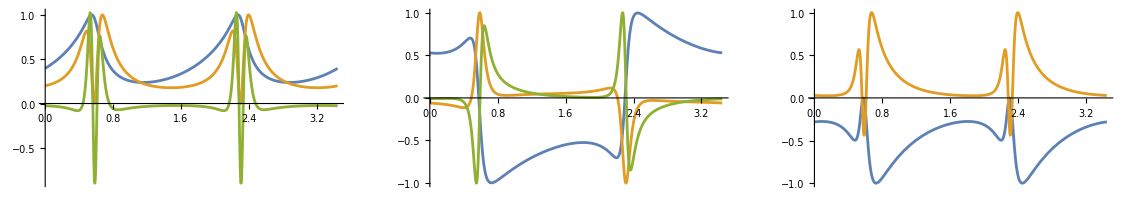

```mathematica
GraphicsRow[{Plot[{intf0[t]/Max[intf0[tgrid]],intf2[t]/Max[intf2[tgrid]],intf4[t]/Max[intf4[tgrid]]},{t,0,Delta},ImageSize->350],Plot[{intu1[t]/Max[intu1[tgrid]],intu2[t]/Max[intu2[tgrid]],intu3[t]/Max[intu3[tgrid]]},{t,0,Delta},ImageSize->350],Plot[{intia22[t]/Max[Abs[intia22[tgrid]]],intia24[t]/Max[Abs[intia24[tgrid]]]},{t,0,Delta},ImageSize->350]}]
```

```mathematica
(*Compute zero of u1*)
```

```mathematica
tau0=t/.FindRoot[intu1[t],{t,0.5}]
```

0.577033

```mathematica
f00=intf0[tau0]
```

0.441418

### Computation(old)

```mathematica
tord=3;
```

```mathematica
alpharepl=Table[Subscript[α, i]->SeriesCoefficient[intu1[t],{t,tau0,i}],{i,0,3}]//Chop
```

{α_0→0,α_1→-222.733,α_2→-376.441,α_3→22779.6}

```mathematica
betarepl=Table[Subscript[β, i]->SeriesCoefficient[intf0[t],{t,tau0,i}],{i,0,3}]
```

{β_0→0.441418,β_1→-1.02034,β_2→-17.5661,β_3→27.8043}

```mathematica
betaser=Subscript[β, 0]+Sum[Subscript[β, i](t-t0)^i,{i,1,tord+3}]
alphaser=Subscript[α, 0]+Sum[Subscript[α, i](t-t0)^i,{i,1,tord+3}]
```

β_0+(t-t0) β_1+(t-t0)^2 β_2+(t-t0)^3 β_3+(t-t0)^4 β_4+(t-t0)^5 β_5+(t-t0)^6 β_6

α_0+(t-t0) α_1+(t-t0)^2 α_2+(t-t0)^3 α_3+(t-t0)^4 α_4+(t-t0)^5 α_5+(t-t0)^6 α_6

```mathematica
replttayl=Join[{psiBC0[t]->Subscript[psi, 0][t],Subscript[f0, 0][t]->betaser,Subscript[u0, 1][t]->alphaser},Table[D[Subscript[f0, 0][t]->betaser,{t,i}],{i,1,tord+2}],Table[D[Subscript[u0, 1][t]->alphaser,{t,i}],{i,1,tord+3}]];
```

#### U_NEC

```mathematica
NEC1=Collect[Series[Series[Uiv0/x,{x,0,tord}]//.replttayl,{t,t0,tord}]//Normal//Expand,{t,x}];
```

```mathematica
(*ord = 1*)
NEC1=NEC1-Coefficient[NEC1,x^1 t^1]*x^1(t-t0)^1//Simplify
```

-(α_0 (x-(-1+dim) β_0)+α_1 (x-(-1+dim) (t-t0) β_0))/((-1+dim) β_0)

```mathematica
(*ord = 2*)
NEC1=NEC1-(1/4 D[NEC1,{x,2},{t,2}]/.t->t0/.x->0)x^2(t-t0)^2-(1/2 D[NEC1,{x,2},t]/.t->t0/.x->0)x^2(t-t0)^1-(1/2 D[NEC1,x,{t,2}]/.t->t0/.x->0)x^1(t-t0)^2;
```

```mathematica
(*ord = 3*)
NEC1=NEC1-(1/(3!*3!)D[NEC1,{x,3},{t,3}]/.t->t0/.x->0)x^3(t-t0)^3-(1/(3!*2!)D[NEC1,{x,3},{t,2}]/.t->t0/.x->0)x^3(t-t0)^2-(1/(3!*1!)D[NEC1,{x,3},{t,1}]/.t->t0/.x->0)x^3(t-t0)^1-(1/(2!*3!)D[NEC1,{x,2},{t,3}]/.t->t0/.x->0)x^2(t-t0)^3-(1/(1!*3!)D[NEC1,{x,1},{t,3}]/.t->t0/.x->0)x^1(t-t0)^3-(1/(2!*2!)D[NEC1,{x,2},{t,2}]/.t->t0/.x->0)x^2(t-t0)^2;
```

```mathematica
(*ord = 4*)
NEC1=(NEC1-Coefficient[NEC1,x^4 t^4] x^4(t-t0)^4-Coefficient[NEC1,x^4 t^3] x^4(t-t0)^3-Coefficient[NEC1,x^4 t^2] x^4(t-t0)^2-Coefficient[NEC1,x^4 t^1] x^4(t-t0)^1-Coefficient[NEC1,x^3 t^4] x^3(t-t0)^4-Coefficient[NEC1,x^2 t^4] x^2(t-t0)^4-Coefficient[NEC1,x^1 t^4] x^1(t-t0)^4);
```

```mathematica
NEC1=Collect[Series[Series[NEC1,{x,0,tord}],{t,t0,tord}]//Normal//Expand,{t,x}];
```

```mathematica
necUvals=NEC1/.t0->tau0/.alpharepl/.betarepl/.dim->4//Simplify
```

-4373.54+22779.6 t^3+t^2 (-39810.2-42026.4 x)-14474.7 x-52913.9 x^2-37996.9 x^3+t (22966.3+49626.7 x+88830.3 x^2)

```mathematica
t/.Solve[NEC1==0,t]//First//FullSimplify
```

(-α_0+t0 α_1+(x (α_0+α_1))/((-1+dim) β_0))/α_1

```mathematica
t/.Solve[necUvals==0,t]//Chop
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0,0,0}

```mathematica
k=Coefficient[%,x]
```

0.755143

```mathematica
ArcTan[k]*180/π
```

37.058

```mathematica
xlist=Range[0,0.01,0.01/50];
```

```mathematica
nec1sol=Table[Solve[(necUvals/.x->xlist[[i]])==0,t,Reals],{i,1,Length[xlist]}]
```

{{{t→0.486069},{t→0.577033},{t→0.684523}},{{t→0.486207},{t→0.577184},{t→0.684603}},{{t→0.486346},{t→0.577335},{t→0.684683}},{{t→0.486486},{t→0.577485},{t→0.684761}},{{t→0.486628},{t→0.577634},{t→0.684839}},{{t→0.486771},{t→0.577784},{t→0.684915}},{{t→0.486915},{t→0.577933},{t→0.684991}},{{t→0.487061},{t→0.578082},{t→0.685065}},{{t→0.487208},{t→0.57823},{t→0.685139}},{{t→0.487357},{t→0.578378},{t→0.685211}},{{t→0.487506},{t→0.578526},{t→0.685283}},{{t→0.487657},{t→0.578673},{t→0.685354}},{{t→0.48781},{t→0.57882},{t→0.685423}},{{t→0.487963},{t→0.578967},{t→0.685492}},{{t→0.488118},{t→0.579113},{t→0.68556}},{{t→0.488275},{t→0.579259},{t→0.685626}},{{t→0.488432},{t→0.579405},{t→0.685692}},{{t→0.488591},{t→0.57955},{t→0.685757}},{{t→0.488752},{t→0.579695},{t→0.68582}},{{t→0.488913},{t→0.579839},{t→0.685883}},{{t→0.489076},{t→0.579984},{t→0.685945}},{{t→0.48924},{t→0.580128},{t→0.686006}},{{t→0.489406},{t→0.580271},{t→0.686065}},{{t→0.489573},{t→0.580415},{t→0.686124}},{{t→0.489741},{t→0.580558},{t→0.686182}},{{t→0.489911},{t→0.580701},{t→0.686238}},{{t→0.490082},{t→0.580843},{t→0.686294}},{{t→0.490254},{t→0.580985},{t→0.686348}},{{t→0.490428},{t→0.581127},{t→0.686402}},{{t→0.490603},{t→0.581268},{t→0.686455}},{{t→0.490779},{t→0.58141},{t→0.686506}},{{t→0.490956},{t→0.581551},{t→0.686557}},{{t→0.491135},{t→0.581691},{t→0.686606}},{{t→0.491316},{t→0.581831},{t→0.686655}},{{t→0.491497},{t→0.581971},{t→0.686702}},{{t→0.49168},{t→0.582111},{t→0.686748}},{{t→0.491865},{t→0.58225},{t→0.686794}},{{t→0.49205},{t→0.58239},{t→0.686838}},{{t→0.492237},{t→0.582528},{t→0.686881}},{{t→0.492426},{t→0.582667},{t→0.686923}},{{t→0.492615},{t→0.582805},{t→0.686964}},{{t→0.492806},{t→0.582943},{t→0.687004}},{{t→0.492999},{t→0.58308},{t→0.687043}},{{t→0.493192},{t→0.583218},{t→0.687081}},{{t→0.493388},{t→0.583355},{t→0.687118}},{{t→0.493584},{t→0.583492},{t→0.687154}},{{t→0.493782},{t→0.583628},{t→0.687188}},{{t→0.493981},{t→0.583764},{t→0.687222}},{{t→0.494182},{t→0.5839},{t→0.687254}},{{t→0.494384},{t→0.584036},{t→0.687286}},{{t→0.494587},{t→0.584171},{t→0.687316}}}

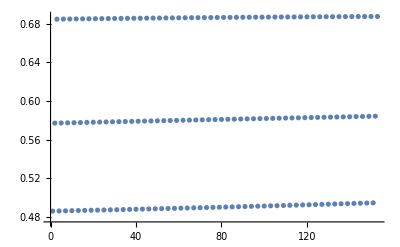

```mathematica
ListPlot[Flatten[nec1sol]//Values]
```

```mathematica
nec1sol[[;;,-1]]
```

{{t→1.35468},{t→1.35501},{t→1.3553},{t→1.35555},{t→1.35575},{t→1.35591},{t→1.35602},{t→1.35607},{t→1.35608},{t→1.35603},{t→1.35592},{t→1.35576},{t→1.35553},{t→1.35523},{t→1.35487},{t→1.35442},{t→1.3539},{t→1.35329},{t→1.35257},{t→1.35175},{t→1.35081},{t→1.34973},{t→1.34849},{t→1.34706},{t→1.34541},{t→1.3435},{t→1.34128},{t→1.33871},{t→1.33591},{t→1.33332},{t→1.33152},{t→1.33053},{t→1.33009},{t→1.32995},{t→1.33},{t→1.33016},{t→1.3304},{t→1.3307},{t→1.33104},{t→1.3314},{t→1.33178},{t→1.33218},{t→1.3326},{t→1.33302},{t→1.33345},{t→1.33389},{t→1.33434},{t→1.33479},{t→1.33524},{t→1.33569},{t→1.33615}}

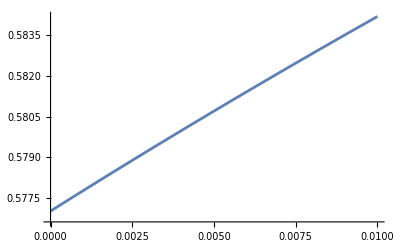

```mathematica
ListPlot[Transpose[{xlist,(nec1sol[[;;,2]])//Values//Flatten}],PlotRange->All,Joined->True]
```

```mathematica
a=Interpolation[Transpose[{xlist,(nec1sol[[;;,2]]//Values//Flatten)*f00}]]
```

InterpolatingFunction[…]

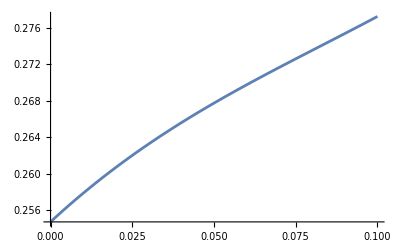

```mathematica
Plot[a[t],{t,0,0.1}]
```

```mathematica
SeriesCoefficient[a[t],{t,0,1}]
```

0.333333

```mathematica
ArcTan[%]*180/π
```

18.4349

#### V_NEC

```mathematica
NEC2=Collect[Series[Series[Viv0/x,{x,0,tord}]//.replttayl,{t,t0,tord}]//Normal//Expand,{t,x}];
```

```mathematica
(*ord = 1*)
NEC2=NEC2-Coefficient[NEC2,x^1 t^1]*x^1(t-t0)^1//Simplify
```

-(α_0 (x-(-1+dim) β_0)+α_1 (x-(-1+dim) (t-t0) β_0))/((-1+dim) β_0)

```mathematica
(*ord = 2*)
NEC2=NEC2-(1/4 D[NEC2,{x,2},{t,2}]/.t->t0/.x->0)x^2(t-t0)^2-(1/2 D[NEC2,{x,2},t]/.t->t0/.x->0)x^2(t-t0)^1-(1/2 D[NEC2,x,{t,2}]/.t->t0/.x->0)x^1(t-t0)^2;
```

```mathematica
(*ord = 3*)
NEC2=NEC2-(1/(3!*3!)D[NEC2,{x,3},{t,3}]/.t->t0/.x->0)x^3(t-t0)^3-(1/(3!*2!)D[NEC2,{x,3},{t,2}]/.t->t0/.x->0)x^3(t-t0)^2-(1/(3!*1!)D[NEC2,{x,3},{t,1}]/.t->t0/.x->0)x^3(t-t0)^1-(1/(2!*3!)D[NEC2,{x,2},{t,3}]/.t->t0/.x->0)x^2(t-t0)^3-(1/(1!*3!)D[NEC2,{x,1},{t,3}]/.t->t0/.x->0)x^1(t-t0)^3-(1/(2!*2!)D[NEC2,{x,2},{t,2}]/.t->t0/.x->0)x^2(t-t0)^2;
```

```mathematica
(*ord = 4*)
NEC1=(NEC1-Coefficient[NEC1,x^4 t^4] x^4(t-t0)^4-Coefficient[NEC1,x^4 t^3] x^4(t-t0)^3-Coefficient[NEC1,x^4 t^2] x^4(t-t0)^2-Coefficient[NEC1,x^4 t^1] x^4(t-t0)^1-Coefficient[NEC1,x^3 t^4] x^3(t-t0)^4-Coefficient[NEC1,x^2 t^4] x^2(t-t0)^4-Coefficient[NEC1,x^1 t^4] x^1(t-t0)^4);
```

```mathematica
NEC2=Collect[Series[Series[NEC2,{x,0,tord}],{t,t0,tord}]//Normal//Expand,{t,x}];
```

```mathematica
necVvals=NEC2/.t0->tau0/.alpharepl/.betarepl/.dim->4//Simplify
```

-4373.54+22779.6 t^3+14474.7 x-52913.9 x^2+37996.9 x^3+t^2 (-39810.2+42026.4 x)+t (22966.3-49626.7 x+88830.3 x^2)

```mathematica
t/.Solve[necVvals==0,t]//First//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.17664+x (0.659893+1760.63 x)-1.74003×10^-32 √(5.63247×10^61+x (-2.81698×10^62+x (-1.52015×10^66+x (7.67458×10^66+1.02381×10^70 x))))

```mathematica
k=Coefficient[%,x]
```

0.755143

```mathematica
ArcTan[k]*180/π
```

37.058

```mathematica
xlist=Range[0,0.01,0.01/50];
```

```mathematica
nec2sol=Table[Solve[(necVvals/.x->xlist[[i]])==0,t,Reals],{i,1,Length[xlist]}]
```

{{{t→0.486069},{t→0.577033},{t→0.684523}},{{t→0.485932},{t→0.576882},{t→0.684442}},{{t→0.485797},{t→0.57673},{t→0.684359}},{{t→0.485663},{t→0.576579},{t→0.684276}},{{t→0.485531},{t→0.576426},{t→0.684192}},{{t→0.4854},{t→0.576273},{t→0.684107}},{{t→0.48527},{t→0.57612},{t→0.684021}},{{t→0.485142},{t→0.575967},{t→0.683934}},{{t→0.485014},{t→0.575813},{t→0.683846}},{{t→0.484889},{t→0.575659},{t→0.683757}},{{t→0.484764},{t→0.575504},{t→0.683667}},{{t→0.484641},{t→0.575349},{t→0.683576}},{{t→0.484519},{t→0.575194},{t→0.683484}},{{t→0.484399},{t→0.575038},{t→0.683392}},{{t→0.48428},{t→0.574882},{t→0.683298}},{{t→0.484162},{t→0.574725},{t→0.683204}},{{t→0.484045},{t→0.574568},{t→0.683108}},{{t→0.48393},{t→0.57441},{t→0.683012}},{{t→0.483817},{t→0.574253},{t→0.682914}},{{t→0.483704},{t→0.574094},{t→0.682816}},{{t→0.483593},{t→0.573936},{t→0.682717}},{{t→0.483484},{t→0.573776},{t→0.682617}},{{t→0.483375},{t→0.573617},{t→0.682516}},{{t→0.483268},{t→0.573457},{t→0.682414}},{{t→0.483163},{t→0.573296},{t→0.682311}},{{t→0.483059},{t→0.573135},{t→0.682207}},{{t→0.482956},{t→0.572974},{t→0.682102}},{{t→0.482854},{t→0.572812},{t→0.681996}},{{t→0.482754},{t→0.57265},{t→0.68189}},{{t→0.482655},{t→0.572487},{t→0.681782}},{{t→0.482558},{t→0.572324},{t→0.681674}},{{t→0.482462},{t→0.57216},{t→0.681565}},{{t→0.482368},{t→0.571996},{t→0.681454}},{{t→0.482274},{t→0.571831},{t→0.681343}},{{t→0.482183},{t→0.571666},{t→0.681231}},{{t→0.482092},{t→0.5715},{t→0.681118}},{{t→0.482003},{t→0.571334},{t→0.681004}},{{t→0.481916},{t→0.571168},{t→0.68089}},{{t→0.481829},{t→0.571001},{t→0.680774}},{{t→0.481745},{t→0.570833},{t→0.680657}},{{t→0.481661},{t→0.570665},{t→0.68054}},{{t→0.481579},{t→0.570496},{t→0.680422}},{{t→0.481499},{t→0.570327},{t→0.680302}},{{t→0.48142},{t→0.570157},{t→0.680182}},{{t→0.481342},{t→0.569987},{t→0.680061}},{{t→0.481266},{t→0.569816},{t→0.679939}},{{t→0.481191},{t→0.569645},{t→0.679816}},{{t→0.481118},{t→0.569473},{t→0.679693}},{{t→0.481046},{t→0.569301},{t→0.679568}},{{t→0.480975},{t→0.569128},{t→0.679442}},{{t→0.480906},{t→0.568954},{t→0.679316}}}

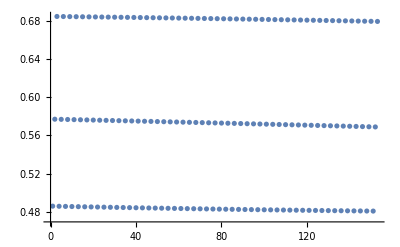

```mathematica
ListPlot[Flatten[nec2sol]//Values]
```

```mathematica
nec2sol[[;;,-1]]
```

{{t→1.35468},{t→1.35501},{t→1.3553},{t→1.35555},{t→1.35575},{t→1.35591},{t→1.35602},{t→1.35607},{t→1.35608},{t→1.35603},{t→1.35592},{t→1.35576},{t→1.35553},{t→1.35523},{t→1.35487},{t→1.35442},{t→1.3539},{t→1.35329},{t→1.35257},{t→1.35175},{t→1.35081},{t→1.34973},{t→1.34849},{t→1.34706},{t→1.34541},{t→1.3435},{t→1.34128},{t→1.33871},{t→1.33591},{t→1.33332},{t→1.33152},{t→1.33053},{t→1.33009},{t→1.32995},{t→1.33},{t→1.33016},{t→1.3304},{t→1.3307},{t→1.33104},{t→1.3314},{t→1.33178},{t→1.33218},{t→1.3326},{t→1.33302},{t→1.33345},{t→1.33389},{t→1.33434},{t→1.33479},{t→1.33524},{t→1.33569},{t→1.33615}}

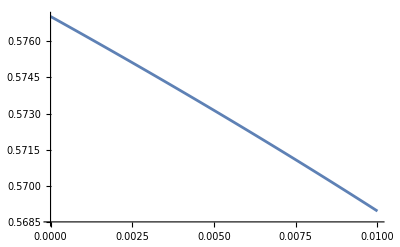

```mathematica
ListPlot[Transpose[{xlist,(nec2sol[[;;,2]])//Values//Flatten}],PlotRange->All,Joined->True]
```

```mathematica
nec2sol[[1,2,1]]//Values
```

0.577033

```mathematica
temp=FindFit[nec2sol[[;;,2]]//Values//Flatten,c0+c1*x+c2*x^2+c3*x^3,{c0,c1,c2,c3},x]
```

{c0→0.577184,c1→-0.000150773,c2→-1.73027×10^-7,c3→-6.84516×10^-10}

```mathematica
VNECpoly[x_]:=(c0+c1*x+c2*x^2+c3*x^3)/.temp
```

```mathematica
VNECpoly[x]
```

0.577184-0.000150773 x-1.73027×10^-7 x^2-6.84516×10^-10 x^3

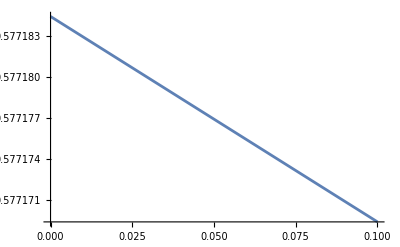

```mathematica
Plot[VNECpoly[x],{x,0,0.1}]
```

```mathematica
b=Interpolation[Transpose[{xlist,(nec2sol[[;;,2]]//Values//Flatten)*f00}]]
```

InterpolatingFunction[…]

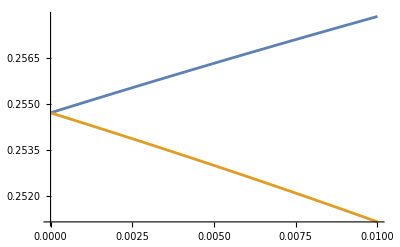

```mathematica
Plot[{a[t],b[t]},{t,0,0.01}]
```

```mathematica
SeriesCoefficient[a[t],{t,0,1}]
```

0.333333

```mathematica
SeriesCoefficient[b[t],{t,0,1}]
```

-0.333333

```mathematica
ArcTan[%]*180/π
```

18.4349